# DG Package com AGC

## 1) Instance Creation and Plot Routines

Instance Creation: DG
DGAllEdges, DGEdgeWeight, DGEdgeDistanceBounds, DGProblem, DGSaveProblem, DGGraphGetIJD

## Source Code

```mathematica
ClearAll[
DGAllEdges,
DGEdgeWeight,
DGEdgeDistanceBounds,
DGProblem,
DGPrintGraph,
DGPrintX,
DGSaveProblem,
DGGraphGetIJD
  ];

DGAllEdges[n_] := Module[{ii, jj, kk = 0, pij},
   pij = Table[0, {ii, (n (n - 1))/2}];
   For[ii = 1, ii <= n, ii++,
    For[jj = (ii + 1), jj <= n, jj++,
      kk++;
      pij[[kk]] = ii <-> jj;
      ];
    ];
   Return[pij]
   ];

DGEdgeWeight[G_, E_] :=
  (* Gets edge weight. 'E' can be a single edge or a list of edges; *)
  Module[
{ii, eij,wij, D = {}},
If[Not[FailureQ[PropertyValue[{G, E[[1]]}, EdgeWeight]]],
(* E is a list of edges *)
For[ii = 1, ii <= Length[E], ii++,
eij = E[[ii]];
If[eij[[1]] > eij[[2]], eij = eij[[2]] <-> eij[[1]]];
If[FailureQ[wij=PropertyValue[{G, eij}, EdgeWeight]],Throw[{"InvalidEdge:",eij}]];
AppendTo[D, wij]],
(* E is a single edge *)
eij = E;
If[eij[[1]] > eij[[2]], eij = eij[[2]] <-> eij[[1]]];
If[FailureQ[D = PropertyValue[{G, E}, EdgeWeight]],Throw[{"InvalidEdge:",eij}]]
];
Return[D]
];

DGEdgeDistanceBounds[G_, E_] := Module[
   {eij = E, Lij, Uij, Vij},
   If[eij[[1]] > eij[[2]], eij = eij[[2]] <-> eij[[1]]];
   Vij = PropertyValue[{G, eij}, "DistanceBounds"];
   Return[Vij]
   ];

DGProblem[x_,eij_: {},dijEps_: {}] :=
  (* Creates a problem P such that P["G"] is the problem graph and P["X"] is a problem solution; *)
  Module[{ii,jj,d,dij,kk,numberOfAtoms,G,E,DijEps},
   (* set default values *)
   If[Length[eij]>0,E=eij,E=DGAllEdges[Length[x]]];
   If[Length[dijEps]>0,DijEps=dijEps,DijEps=Table[0,{ii,Length[E]}]];
   (* unpacks the edges and calculate distances *)
   ii=Table[E[[kk]][[1]],{kk,Length[E]}];
   jj=Table[E[[kk]][[2]],{kk,Length[E]}];
   d=Table[N[Norm[x[[ii[[kk]]]] - x[[jj[[kk]]]]]], {kk, Length[E]}];
   numberOfAtoms = Max[ii, jj];
   (* creates distance matrix *)
   G=Table[Infinity, {ii, 1, numberOfAtoms}, {jj, 1, numberOfAtoms}];
   For[kk=1,kk≤Length[ii],kk++,
      G[[ii[[kk]]]][[jj[[kk]]]]=d[[kk]];
      G[[jj[[kk]]]][[ii[[kk]]]]=d[[kk]]
    ];
   (* creates the graph *)
   G = WeightedAdjacencyGraph[G];
   (* adds distance bounds *)
   If[Length[DijEps]!=Length[ii],Throw["InvalidInput: eij and dijEps must have the same size"]]; 
   For[kk=1,kk≤Length[ii],kk++,
    dij=DGEdgeWeight[G,ii[[kk]]<->jj[[kk]]];
    PropertyValue[{G,ii[[kk]]<->jj[[kk]]},"DistanceBounds"]={(1-DijEps[[kk]]),(1+DijEps[[kk]])}*dij
    ];
   Return[<|"X"->x,"G"->G|>]
   ];

DGPrintGraph[G_]:=Module[{edges,table,eij,ii,jj,kk,Lij,Uij,Dij},
edges=EdgeList[G];
table=Table[0,{ii,Length[edges]},{jj,5}];
For[kk=1,kk≤Length[edges],kk++,
eij=edges[[kk]];
{ii,jj}={eij[[1]],eij[[2]]};
{Lij,Uij}=DGEdgeDistanceBounds[G,eij];
Dij=DGEdgeWeight[G,eij];
table[[kk]]={ii,jj,Dij,Lij,Uij}
];
Print[TableForm[table,TableHeadings->{Table[ii,{ii,Length[edges]}],{"ii","jj","dij","lij","uij"}}]]
];

DGPrintX[X_]:=Print[TableForm[X, TableHeadings -> {Table[ii, {ii, Length[X]}], {"x", "y", "z"}}]]; 

DGPrintDistanceMatrix[X_,edges_]:=Module[{E=edges,table,ii,jj,kk},
table=Table[{ii=E[[kk]][[1]],jj=E[[kk]][[2]],N[Norm[X[[ii]]-X[[jj]]]]},{kk,Length[E]}];
Print[TableForm[table,TableHeadings->{Table[ii,{ii,Length[E]}], {"ii","jj","dij"}}]]
];
DGPrintDistanceMatrix[X_]:=Module[{edges},
edges=DGAllEdges[Length[X]];
DGPrintDistanceMatrix[X,edges]
];

DGSaveProblem[P_, fname_] :=
  (* Create the files fname.csv and fname_xsol.csv with, respectively, the DG constraints given by P["G"] and one associated solution P["X"] *)
  Module[{edges, fid, table, eij, ii, jj, kk, X, G, Dij, Lij, Uij},
   (* creates and saves solution table *)
   table = Table[P["X"][[ii]][[jj]], {ii, Length[P["X"]]}, {jj, 3}];
   fid = StringJoin[fname, "_xsol.csv"];
   Print["Saving solution file ", fid];
   Export[fid, table, TableHeadings -> {"x", "y", "z"}];
   (* creates and saves constraints table *)
   G = P["G"];
   edges = EdgeList[G];
   table = Table[0, {ii, Length[edges]}, {jj, 5}];
   For[kk = 1, kk <= Length[edges], kk++,
    eij = edges[[kk]];
    {ii, jj} = {eij[[1]], eij[[2]]};
    {Lij, Uij} = DGEdgeDistanceBounds[G, eij];
    Dij = DGEdgeWeight[G, eij];
    table[[kk]] = {ii, jj, N[Dij], N[Lij], N[Uij]}
    ];
   fid = StringJoin[fname, ".csv"];
   Print["Saving constraints file ", fid];
   Export[fid, table, TableHeadings -> {"I", "J", "D", "L", "U"}];
   ];

DGGraphGetIJD[G_]:=Module[{ii,jj,kk,d,E},
E=EdgeList[G];
ii=Table[E[[kk]][[1]],{kk,Length[E]}];
jj=Table[E[[kk]][[2]],{kk,Length[E]}];
d=Table[DGEdgeWeight[G,E[[kk]]],{kk,Length[E]}];
Return[{ii,jj,d}];
]
```

## Examples:

```mathematica
(* DGAllEdges *)
DGAllEdges[4]
```

{1<->2,1<->3,1<->4,2<->3,2<->4,3<->4}

```mathematica
(* Creates a DGProblem with complete graph *)
x = {{0, 0, 0}, {1, 0, 0}, {0, 1, 0}, {1, 1, 1}, {0, 1, 1}};
P = DGProblem[x];
DGPrintGraph[P["G"]]
DGPrintDistanceMatrix[x]
```

| ii | jj | dij | lij | uij
1 | 1 | 2 | 1. | 1. | 1.
2 | 1 | 3 | 1. | 1. | 1.
3 | 1 | 4 | 1.73205 | 1.73205 | 1.73205
4 | 1 | 5 | 1.41421 | 1.41421 | 1.41421
5 | 2 | 3 | 1.41421 | 1.41421 | 1.41421
6 | 2 | 4 | 1.41421 | 1.41421 | 1.41421
7 | 2 | 5 | 1.73205 | 1.73205 | 1.73205
8 | 3 | 4 | 1.41421 | 1.41421 | 1.41421
9 | 3 | 5 | 1. | 1. | 1.
10 | 4 | 5 | 1. | 1. | 1.

| ii | jj | dij
1 | 1 | 2 | 1.
2 | 1 | 3 | 1.
3 | 1 | 4 | 1.73205
4 | 1 | 5 | 1.41421
5 | 2 | 3 | 1.41421
6 | 2 | 4 | 1.41421
7 | 2 | 5 | 1.73205
8 | 3 | 4 | 1.41421
9 | 3 | 5 | 1.
10 | 4 | 5 | 1.

```mathematica
(* Creates a DGProblem with specific edges *)
x = {{0, 0, 0}, {1, 0, 0}, {0, 1, 0}, {1, 1, 1}, {0, 1, 1}};
eij = {1 <-> 2, 2 <-> 3, 3 <-> 4, 4 <-> 5};
P = DGProblem[x, eij]; 
DGPrintGraph[P["G"]]
```

| ii | jj | dij | lij | uij
1 | 1 | 2 | 1. | 1. | 1.
2 | 2 | 3 | 1.41421 | 1.41421 | 1.41421
3 | 3 | 4 | 1.41421 | 1.41421 | 1.41421
4 | 4 | 5 | 1. | 1. | 1.

```mathematica
(* Creates a DGProblem with inexact distances *)
x = {{0, 0, 0}, {1, 0, 0}, {0, 1, 0}, {1, 1, 1}, {0, 1, 1}};
eij = {1<->2, 2<->3, 3<->4, 4<->5};
dijEps = {0, 0.1, 0, 0.2};
P = DGProblem[x, eij, dijEps];
DGPrintGraph[P["G"]]
```

| ii | jj | dij | lij | uij
1 | 1 | 2 | 1. | 1. | 1.
2 | 2 | 3 | 1.41421 | 1.27279 | 1.55563
3 | 3 | 4 | 1.41421 | 1.41421 | 1.41421
4 | 4 | 5 | 1. | 0.8 | 1.2

```mathematica
(* Saves a DGProblem *)
x = {{0, 0, 0}, {1, 0, 0}, {0, 1, 0}, {1, 1, 1}, {0, 1, 1}};
P = DGProblem[x];
DGSaveProblem[P, "d:\\_testesWolfram"]
```

Saving solution file d:\_testesWolfram_xsol.csv

Saving constraints file d:\_testesWolfram.csv

Instance Creation: MDGP
DGSetXByCartesianSystem, DGSetXByHomogeneousCoords, DGRandom3DBackbone, DGRandomMDGP, DGCalculateProteinAngles, DGCalculateProteinAnglesForAtomAtPosition, DGCalculateTorsionAngles

## Source Code

```mathematica
ClearAll[
DGSetXByCartesianSystem,
DGSetXByHomogeneousCoords,
DGRandom3DBackbone,
DGRandomMDGP,
DGPlaneAndTorsionAngles
];
DGSetXByCartesianSystem[d_,θ_,ω_]:=
(* Calculates Euclidean coords from distances, planar and dihedral angles using rotations and translations explicitly;
   Input parameters;
   d: distances       (d[i] = norm(x[[i]]-x[[i-1]]));            
   θ: planar angles   (θ[i] = angle(x[i],x[i-1],x[i-2]));        
   ω: dihedral angles (ω[i] = angle(x[i],x[i-1],x[i-2],x[i-3]) 
*)
Module[
(* declare local variables *)
{a,b,c,ii,v,n,R,X,numberOfAtoms},
numberOfAtoms=Length[d];
(* atoms positions on Euclidean 3d space *)
X=Table[0,{ii,numberOfAtoms},{jj,3}];
(* set the position of the three first points *)
X[[{1,2,3}]]={{0,0,0},{-d[[2]],0,0},{-d[[2]]+d[[3]]Cos[θ[[3]]],d[[3]]Sin[θ[[3]]] ,0}};
(* set remaining positions *)
For[ii=4,ii≤numberOfAtoms,ii++,
{a,b,c}={X[[ii-3]],X[[ii-2]],X[[ii-1]]};
v= d[[ii]]* Normalize[b-c]; 
(* normal to the plane abc *)
n=Cross[a-b,c-b];
(* apply plane rotation *)
R=RotationTransform[θ[[ii]],n]; (* rotation creation *)
v=R[v]; (* rotation apply *)
(* apply torsion rotation and translation *)
R=RotationTransform[ω[[ii]],c-b];
v=R[v]+c;
(* set i-th coordinate *)
X[[ii]]=v
];
Return[X]
];

DGSetXByHomogeneousCoords[d_,θ_,ω_]:=
(* Calculates Euclidean coords from distances, planar and dihedral angles using transformation matrices;
   Input parameters;
   d: distances       (d[i] = norm(x[[i]]-x[[i-1]]));            
   θ: planar angles   (θ[i] = angle(x[i],x[i-1],x[i-2]));        
   ω: dihedral angles (ω[i] = angle(x[i],x[i-1],x[i-2],x[i-3]); 
*)
Module[
{B,B1,B2,B3,X,ii,di,ct,st,cw,sw,v,numberOfAtoms},
numberOfAtoms=Length[d];
(* atoms positions on Euclidean 3d space *)
X=Table[0,{ii,numberOfAtoms},{jj,3}];
(* set the position of the three first points *)
{ct,st}={Cos[θ[[3]]],Sin[θ[[3]]]};
X[[{1,2,3}]]={{0,0,0},{-d[[2]],0,0},{-d[[2]]+d[[3]]ct,d[[3]]st ,0}};
(* set first transformation matrices *)
B1=IdentityMatrix[4];
B2={{-1,0,0,-d[[2]]},{0,1,0,0},{0,0,-1,0},{0,0,0,1}};
di=d[[3]];
B3={{-ct,-st,0,-di*ct},{st,-ct,0,di*st},{0,0,1,0},{0,0,0,1}};
(* set remaining coordinates *)
B=B1.B2.B3;
For[ii=4,ii≤numberOfAtoms,ii++,
{ct,st}={Cos[θ[[ii]]],Sin[θ[[ii]]]};
{cw,sw}={Cos[ω[[ii]]],Sin[ω[[ii]]]};
di=d[[ii]];
(* concatenate transformation matrices *)
B =B.{{-ct,-st,0,-di*ct},{st*cw,-ct*cw,-sw,di*st*cw},{st*sw,-ct*sw,cw,di*st*sw},{0,0,0,1}};
(* apply transformation at origin *)
v =B.{0,0,0,1};
(* update coordinate *)
X[[ii]]=v[[{1,2,3}]];
];
Return[X]
];

DGRandom3DBackbone[numberOfAtoms_,algorithm_:"HomogeneousCoords",seed_:0]:=
(* Generates a random backbone in tridimensional Euclidean space;
   Input parameters;
   numberOfAtoms: number of 3D Euclidean points to be generated;
   algorithm: algorithm to be applied during coordinates calculation. The options 'are HomogeneousCoords' or 'CartesianSystem';
   seed: integer number used to reproduce random sequence generation. If seed=0 a sequence based on the current time is constructed;
 *)
Module[
(* declare the local variables *)
{d,θ,ω,X,output,ϵ=0.05},
(* set seed *)
If[seed>0,SeedRandom[seed]];
(* length of covalent bonds *)
d=Table[1.526,{ii,numberOfAtoms}];
d[[1]]=0;
(* plane angles *)
θ=Table[1.91,{ii,numberOfAtoms}];
θ[[{1,2}]]={0,0};
(* torsion angles *)
ω=Table[RandomChoice[{60Degree,180Degree,300Degree}]*(1+RandomReal[{-ϵ,ϵ}]),{ii,numberOfAtoms}];
ω[[{1,2,3}]]={0,0,0};
(* set the remaining 3d positions *)
Switch[algorithm,
"HomogeneousCoords",X=DGSetXByHomogeneousCoords[d,θ,ω],
"CartesianSystem",X=DGSetXByCartesianSystem[d,θ,ω],
_,Throw["InvalidAlgorithm:",OptionValue[algorithm]]
];
(* set output *)
<|"Points"->X,"TorsionAngles"->ω,"CovalentBondLengths"->d,"PlaneRotationAngles"->θ|>
];

DGEdgesMDGP[numberOfAtoms_]:=Module[{ii,jj,edges={}},
For[ii=1,ii≤numberOfAtoms,ii++,
For[jj=ii+1,jj≤Min[ii+3,numberOfAtoms],jj++,
AppendTo[edges,ii<->jj];
];
];
Return[edges]
];

DGRandomMDGP[numberOfAtoms_,dijEps_:0.0,dijMax_:Infinity,seed_:0]:=
(* Generates a random MDGP instance.; 
   numberOfAtoms: number of 3D Euclidean points to be generated;
   dijEps: the upper (uij) and lower (lij) constraints boundaries are generated using the formulae lij = (1-dijEps) and uij = (1+dijEps); 
   dijMax: all distances greater than dijMax are dropped;
   algorithm: defines the method (algorithm) used to calculate the pairwise distances. The options are "DistanceMatrix" and "Nearest";
   seed: integer number used to reproduce random sequence generation. If seed=0 a sequence based on current is constructed;
*)
Module[
(* declare local variables *)
{ii,jj,X,D,E,dij,DijEps},
X=DGRandom3DBackbone[numberOfAtoms,"HomogeneousCoords",seed]["Points"];
E={};
DijEps={};
(* set distance bounds *)
For[ii=1,ii≤numberOfAtoms,ii++,
For[jj=ii+1,jj≤numberOfAtoms,jj++,
(* exact distances *)
If[Abs[ii-jj]≤2,
AppendTo[E,{ii,jj}];
AppendTo[DijEps,0];
Continue[];
];
(* intervalar distances *)
If[Abs[ii-jj]==3||N[Norm[X[[ii]]-X[[jj]]]]<dijMax,
AppendTo[E,{ii,jj}];
AppendTo[DijEps,dijEps]
];
];
];
Return[DGProblem[X,E,DijEps]]
];

DGPlaneAndTorsionAngles[A_,B_,C_,D_,verbose_:False]:=
(* Calculates the plane and torsion for 3D points A, B, C and D in that order. *)
Module[
{nabc, nbcd,θ,ω},
(* centered at C *)
θ=VectorAngle[B-C,D-C];
If[verbose,Print["(θ):Angle[BCD]  =",θ]];
(* centered at B and C *)
{nabc,nbcd} = {Cross[A-B,C-B],Cross[B-C,D-C]};
ω=VectorAngle[nabc,nbcd];
If[verbose,Print["(ω):Angle[ABCD] =",ω]];
Return[{θ,ω}];
];

DGPlaneAndTorsionAngles[X_,ii_]:=
(* Calculates plane and torsion angles of i-th atom. *)
DGPlaneAndTorsionAngles[X[[ii-3]],X[[ii-2]],X[[ii-1]],X[[ii]]];

DGPlaneAndTorsionAngles[X_]:=Module[
{θ,ω,ii},
ω=Table[0,{ii,Length[X]}];
θ=Table[0,{ii,Length[X]}];
For[ii=4,ii≤Length[X],ii++,
{θ[[ii]],ω[[ii]]}=DGPlaneAndTorsionAngles[X,ii]
];
Return[{θ,ω}]
];
```

## Examples

```mathematica
(* MDGP Edges *)
DGEdgesMDGP[5]
```

{1<->2,1<->3,1<->4,2<->3,2<->4,2<->5,3<->4,3<->5,4<->5}

```mathematica
(* Calculates plane and torsion angles *)
x={{0,0,1},{0,0,0},{0,1,0},{1,1,1},{0,1,1}};
{θ,ω}=DGPlaneAndTorsionAngles[x[[1]],x[[2]],x[[3]],x[[4]]]
```

{π/2,π/4}

```mathematica
x={{0,0,1},{0,0,0},{0,1,0},{1,1,1},{0,1,1}};
{θ,ω}=DGPlaneAndTorsionAngles[x,4]
```

{π/2,π/4}

```mathematica
x={{0,0,1},{0,0,0},{0,1,0},{1,1,1},{0,1,1}};
{θ,ω}=DGPlaneAndTorsionAngles[x]
```

{{0,0,0,π/2,π/4},{0,0,0,π/4,π/2}}

```mathematica
(* Creates a random backbone *)
x=DGRandom3DBackbone[5,"HomogeneousCoords",0]
```

<|Points→{{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-1.56394,2.14325,-1.26966},{-2.05823,3.58696,-1.2621}},TorsionAngles→{0,0,0,1.08072,3.1528},CovalentBondLengths→{0,1.526,1.526,1.526,1.526},PlaneRotationAngles→{0,0,1.91,1.91,1.91}|>

```mathematica
(* Creates a MDGP random instance with exact distances *)
P=DGRandomMDGP[5];
DGPrintGraph[P["G"]]
```

| ii | jj | dij | lij | uij
1 | 1 | 2 | 1.526 | 1.526 | 1.526
2 | 1 | 3 | 2.49139 | 2.49139 | 2.49139
3 | 1 | 4 | 3.83356 | 3.83356 | 3.83356
4 | 1 | 5 | 4.25221 | 4.25221 | 4.25221
5 | 2 | 3 | 1.526 | 1.526 | 1.526
6 | 2 | 4 | 2.49139 | 2.49139 | 2.49139
7 | 2 | 5 | 2.934 | 2.934 | 2.934
8 | 3 | 4 | 1.526 | 1.526 | 1.526
9 | 3 | 5 | 2.49139 | 2.49139 | 2.49139
10 | 4 | 5 | 1.526 | 1.526 | 1.526

```mathematica
(* Creates a MDGP random instance with inexact distances *)
P=DGRandomMDGP[5,0.1,5.0];
Norm[P["X"][[1]]-P["X"][[5]]]
DGPrintGraph[P["G"]]
```

4.27185

| ii | jj | dij | lij | uij
1 | 1 | 2 | 1.526 | 1.526 | 1.526
2 | 1 | 3 | 2.49139 | 2.49139 | 2.49139
3 | 1 | 4 | 3.83709 | 3.45338 | 4.2208
4 | 1 | 5 | 4.27185 | 3.84467 | 4.69904
5 | 2 | 3 | 1.526 | 1.526 | 1.526
6 | 2 | 4 | 2.49139 | 2.49139 | 2.49139
7 | 2 | 5 | 2.92239 | 2.63015 | 3.21463
8 | 3 | 4 | 1.526 | 1.526 | 1.526
9 | 3 | 5 | 2.49139 | 2.49139 | 2.49139
10 | 4 | 5 | 1.526 | 1.526 | 1.526

Plot Routines
DGPlot3DBackbone, DGPlotAdjacencyMatrix

## Source Code

```mathematica
ClearAll[
DGPlot3DBackbone,
DGPlotAdjacencyMatrix
]

DGPlot3DBackbone[X_,r_,d_]:=Module[{objs={},single,kk,ii,Y},
(* Plots the points using the coordinates of X["Points"] property *)
single=Length[X[[1]][[1]]]==0;
If[single,Y={X},Y=X];
For[kk=1,kk≤Length[Y],kk++,
objs=Union[objs,Table[{Red,Sphere[Y[[kk]][[ii]],r]},{ii,3}]];
objs=Union[objs,Table[{Blue,Sphere[Y[[kk]][[ii]],r]},{ii,3,Length[Y[[kk]]]}]];
AppendTo[objs,{LightGray,Tube[Y[[kk]],d]}];
];
Graphics3D[
objs,
 Axes->False,
Boxed->False]
]

DGPlotAdjacencyMatrix[G_,DiagonalCovering_:False]:=Module[
{ii,jj,n,ei,ej,edges,primitives,add},
n=Max[VertexList[G]];
edges=EdgeList[G];
(* inverting edges position *)
edges=Table[{edges[[ii]][[2]],n-edges[[ii]][[1]]+1},{ii,Length[edges]}];
primitives={
{PointSize[Medium],Point[edges]},
{Red,Dashed,Line[{{1,n},{n,1}}]}
};
(* Plot diagonal covering *)
If[DiagonalCovering,
For[ii=1,ii≤Length[edges],ii++,
add=True;
ei=edges[[ii]];
For[jj=1,jj≤Length[edges],jj++,
ej=edges[[jj]];
If[(ej[[1]]==ei[[1]]&&ej[[2]]>ei[[2]]),add=False];
If[(ej[[2]]==ei[[2]]&&ej[[1]]>ei[[1]]),add=False];
];
If[add,
PrependTo[primitives,
{Opacity[0.2],Red,Triangle[{{ei[[1]],n+1-ei[[1]]},ei,{n+1-ei[[2]],ei[[2]]}}]}]
];
];
];
Graphics[primitives,
Axes->True,
GridLines->Automatic,
Ticks->{Automatic,Table[{ii,n+1-ii},{ii,n}]},
AxesOrigin->{1,1}
]
];
```

## Examples

```mathematica
(* Plot a simple a backbone *)
x=DGRandom3DBackbone[7];
DGPlot3DBackbone[x["Points"],0.1,0.04]
```

-Graphics3D-

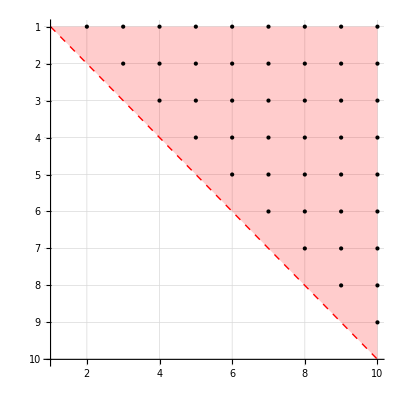

```mathematica
(* Plot adjacency matrix *)
P=DGRandomMDGP[10];
DGPlotAdjacencyMatrix[P["G"],True]
```

## 2) Check Solution and Standard Solvers

Solution Analysis 
DGRelativeResidue, DGLDME, DGRMSD

## Source Code

```mathematica
ClearAll[DGRelativeResidue,DGRMSD,DGLDME,DGMDEE]
DGRelativeResidue[G_,X_,verbose_:False]:=Module[
{ii,jj,kk,lij,uij, dij,numberOfEdges,E,error},
E=EdgeList[P["G"]];
numberOfEdges=Length[E];
error=Table[0,{ii,numberOfEdges}];
For[kk=1,kk≤numberOfEdges,kk++,
{ii=E[[kk]][[1]],jj=E[[kk]][[2]]};
{lij,uij}=DGEdgeDistanceBounds[G,ii<->jj];
dij=Norm[X[[ii]]-X[[jj]]];
error[[kk]]=Max[Max[{0,lij-dij}]/lij,Max[{0,dij-uij}]/uij];
];
If[verbose,
Print["Solution Quality"];
Print["Number of nodes      : ",Length[X]];
Print["Number of edges      : ",Length[E]];
Print["Relative error bounds: ",{Min[error],Max[error]}];
Print["Mean relative error  : ",Mean[error]]];
Return[{error,Mean[error]}];
];

DGRelativeResidue[G_,X_,nodes_,ii_]:=
(* Calculates the relative residue of the nodes[[i]] considering only the nodes[[1;;i-1]] *)
Module[
(* local variables *)
{eij,jj,kk,V,Xi,Xj,Dij,Lij,Uij,errorDij,nid},
(* current position *)
Xi=X[[nodes[[ii]]]];
(* indentifies which nodes has been already fixed *)
nid=Table[0,{kk,ii}];
For[kk=1,kk≤ii,kk++,
nid[[nodes[[kk]]]]=kk
];
(* considering only the precedent nodes *)
V= Select[AdjacencyList[G,nodes[[ii]]],MemberQ[nid,#]&];
(*Print["V=",V];*)
errorDij=0.0;
For[kk=1,kk≤Length[V],kk++,
(* neighbor index *)
jj=V[[kk]];
(* neighbor coordinate *)
Xj=X[[jj]];
(* actual distance *)
Dij=EuclideanDistance[Xi,Xj];
(* distance bounds *)
{Lij,Uij}=DGEdgeDistanceBounds[G,ii<->jj];
(* error Dij *)
eij=Max[(Lij-Dij)/Lij,(Dij-Uij)/Uij];
(* update error *)
If[eij>errorDij,errorDij=eij];
];
Return[errorDij]
];

DGLDME[G_,X_]:=Module[
{ii,jj,kk,E,ldme=0,lij,uij,dij},
E=EdgeList[G];
For[kk=1,kk≤Length[E],kk++,
{lij,uij}=DGEdgeDistanceBounds[G,E[[kk]]];
ii=E[[kk]][[1]];
jj=E[[kk]][[2]];
dij=Norm[X[[ii]]-X[[jj]],2];
ldme+=Max[lij-dij,dij-uij,0]^2
];
Return[Sqrt[ldme/Length[E]]]
];

DGMDEE[G_,X_]:=Module[
{ii,jj,kk,E,mdee=0,lij,uij,dij},
E=EdgeList[G];
For[kk=1,kk≤Length[E],kk++,
{lij,uij}=DGEdgeDistanceBounds[G,E[[kk]]];
ii=E[[kk]][[1]];
jj=E[[kk]][[2]];
dij=Norm[X[[ii]]-X[[jj]],2];
mdee+=Max[lij-dij,dij-uij,0]/uij;
];
Return[Sqrt[mdee/Length[E]]]
];


DGRMSD[X_,Y_]:=Module[
{xc,yc,x,y,ii,U,D,V,rmsd},
(* calculating centers *)
xc=Mean[X];
yc=Mean[Y];
(* translation *)
x=Table[X[[ii]]-xc,{ii,Length[X]}];
y=Table[Y[[ii]]-yc,{ii,Length[Y]}];
(* svd *)
V=Transpose[x].y;
{U,D,V}=SingularValueDecomposition[V];
V=U.Transpose[V];
x=x.V;
rmsd=Norm[x-y,"Frobenius"]/Sqrt[Length[x]];
Return[{rmsd,V,x,y}]
]
```

## Examples

```mathematica
(* DGRMSD *)
X={{0.814700,0.097500,0.157600},{0.905800,0.278500,0.970600},{0.127000,0.546900,0.957200},{0.913400,0.957500,0.485400},{0.632400,0.964900,0.800300}};
Y={{6.167723,5.509229,5.376972},{5.921716,5.625914,6.161379},{5.265461,5.705450,6.339958},{5.936486,6.432611,5.883000},{5.680966,5.982123,5.893736}};
{MatrixForm[X],MatrixForm[Y]}
{rmsd,Q,x,y}=DGRMSD[X,Y];
{rmsd,MatrixForm[Q],MatrixForm[x],MatrixForm[y]}
```

{(0.8147 | 0.0975 | 0.1576
0.9058 | 0.2785 | 0.9706
0.127 | 0.5469 | 0.9572
0.9134 | 0.9575 | 0.4854
0.6324 | 0.9649 | 0.8003),(6.16772 | 5.50923 | 5.37697
5.92172 | 5.62591 | 6.16138
5.26546 | 5.70545 | 6.33996
5.93649 | 6.43261 | 5.883
5.68097 | 5.98212 | 5.89374)}

{0.190378,(0.956675 | 0.276543 | 0.091089
-0.283739 | 0.955674 | 0.0786132
-0.0653114 | -0.101053 | 0.992735),(0.297687 | -0.360831 | -0.537546
0.280385 | -0.244816 | 0.292075
-0.539953 | -0.202332 | 0.228932
0.126686 | 0.455218 | -0.135529
-0.164806 | 0.35276 | 0.152068),(0.373253 | -0.341836 | -0.554037
0.127246 | -0.225151 | 0.23037
-0.529009 | -0.145615 | 0.408949
0.142016 | 0.581546 | -0.048009
-0.113504 | 0.131058 | -0.037273)}

```mathematica
(* Check relative error *)
x = {{0, 0, 0}, {1, 0, 0}, {0, 1, 0}, {1, 1, 1}, {0, 1, 1}};
P = DGProblem[x];
DGRelativeResidue[P["G"],x,True]
DGRelativeResidue[P["G"],x+RandomReal[0.1,Length[x]],True]
```

Solution Quality

Number of nodes      : 5

Number of edges      : 10

Relative error bounds: {0.,0.}

Mean relative error  : 0.

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},0.}

Solution Quality

Number of nodes      : 5

Number of edges      : 10

Relative error bounds: {0.00156003,0.0957747}

Mean relative error  : 0.0369687

{{0.0257453,0.0665058,0.0216772,0.00273521,0.00156003,0.0486943,0.00815735,0.0957747,0.0738411,0.0249959},0.0369687}

```mathematica
x = {{0, 0, 0}, {1, 0, 0}, {0, 1, 0}, {1, 1, 1}, {0, 1, 1}};
P = DGProblem[x];
x[[4]]+=0.1;
DGRelativeResidue[P["G"],x,{1,2,3,4,5},4]
```

0.10227

General Methods
DGNSolve, DGAllEdgesSolver, DGOptSolver

## DGNSolve - Nonlinear equations

### Source Code

```mathematica
ClearAll[DGNSolve]
DGNSolve[G_]:=Module[{kk,ii,jj,d,d12,eqs,xi,xj,x,n},
{ii,jj,d}=DGGraphGetIJD[G];
eqs=Table[0,{k,Length[ii]}];
n=Max[ii,jj];
x=Table[Symbol[StringJoin["x",ToString[xi],ToString[xj]]],{xi,n},{xj,3}];
For[kk=1,kk≤Length[ii],kk++,
xi=x[[ii[[kk]]]];
xj=x[[jj[[kk]]]];
eqs[[kk]]=(xi[[1]]-xj[[1]])^2+(xi[[2]]-xj[[2]])^2+(xi[[3]]-xj[[3]])^2==d[[kk]]^2
];
(* set some points *)
d12=DGEdgeWeight[G,1<->2];
eqs=Join[eqs,
{x[[1]][[1]]==0,x[[1]][[2]]==0,x[[1]][[3]]==0,
x[[2]][[1]]==d12,x[[2]][[2]]==0,x[[2]][[3]]==0}
];
Print["eqs=",TableForm[eqs]];
x=Flatten[x];
Quiet[x=NSolve[eqs,x,Reals]];
x=ArrayReshape[x,{n,3}];
Print["x=",TableForm[x]];
(* convert relations to scalar matrix *)
If[Length[x[[1]][[1]]]>1,x=Table[x[[ii]][[jj]][[2]],{ii,n},{jj,3}]];
Return[x]
];
```

### Examples

#### Example: 5 points and 4 constraints

```mathematica
x={{0,0,0},{1,0,0},{0,1,0},{0,0,1},{1,1,0}};
eij={{1,2},{1,3},{2,3},{2,5}};
P=DGProblem[x,eij];
DGPrintGraph[P["G"]];
x=DGNSolve[P["G"]];
TableForm[x,TableHeadings->{Table[ii,{ii,Length[x]}],{"x","y","z"}}]
DGRelativeResidue[P["G"],x,True];
```

| ii | jj | dij | lij | uij
1 | 1 | 2 | 1. | 1. | 1.
2 | 1 | 3 | 1. | 1. | 1.
3 | 2 | 3 | 1.41421 | 1.41421 | 1.41421
4 | 2 | 5 | 1. | 1. | 1.

eqs=(x11-x21)^2+(x12-x22)^2+(x13-x23)^2==1.
(x11-x31)^2+(x12-x32)^2+(x13-x33)^2==1.
(x21-x31)^2+(x22-x32)^2+(x23-x33)^2==2.
(x21-x51)^2+(x22-x52)^2+(x23-x53)^2==1.
x11==0
x12==0
x13==0
x21==1.
x22==0
x23==0

x=0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0

| x | y | z
1 | 0 | 0 | 0
2 | 0 | 0 | 0
3 | 0 | 0 | 0
4 | 0 | 0 | 0
5 | 0 | 0 | 0

Solution Quality

Number of nodes      : 5

Number of edges      : 4

Relative error bounds: {1.,1.}

Mean relative error  : 1.

#### Example: 5 points and 4 constraints (failed)

```mathematica
x={
{0.732761,0.169653,0.656641},
{0.246863,0.660452,0.742898},
{0.426759,0.729058,0.897434},
{0.100975,0.670080,0.241258},
{0.204643,0.236955,0.655968}
};
eij={{1,2},{1,3},{2,3},{2,5}};
P=DGProblem[x,eij];
DGPrintGraph[P["G"]];
x=DGNSolve[P["G"]];
DGRelativeResidue[P["G"],x,True];
```

| ii | jj | dij | lij | uij
1 | 1 | 2 | 0.696003 | 0.696003 | 0.696003
2 | 1 | 3 | 0.681581 | 0.681581 | 0.681581
3 | 2 | 3 | 0.246882 | 0.246882 | 0.246882
4 | 2 | 5 | 0.434384 | 0.434384 | 0.434384

eqs=(x11-x21)^2+(x12-x22)^2+(x13-x23)^2==0.484421
(x11-x31)^2+(x12-x32)^2+(x13-x33)^2==0.464552
(x21-x31)^2+(x22-x32)^2+(x23-x33)^2==0.0609507
(x21-x51)^2+(x22-x52)^2+(x23-x53)^2==0.188689
x11==0
x12==0
x13==0
x21==0.696003
x22==0
x23==0

x=0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0

Solution Quality

Number of nodes      : 5

Number of edges      : 4

Relative error bounds: {1.,1.}

Mean relative error  : 1.

#### Example: 5 points and all constraints

```mathematica
x={{0,0,0},{1,0,0},{0,1,0},{0,0,1},{1,1,0}};
P=DGProblem[x];
DGPrintGraph[P["G"]];
x=DGNSolve[P["G"]];
TableForm[x,TableHeadings->{Table[ii,{ii,Length[x]}],{"x","y","z"}}]
DGRelativeResidue[P["G"],x,True];
```

| ii | jj | dij | lij | uij
1 | 1 | 2 | 1. | 1. | 1.
2 | 1 | 3 | 1. | 1. | 1.
3 | 1 | 4 | 1. | 1. | 1.
4 | 1 | 5 | 1.41421 | 1.41421 | 1.41421
5 | 2 | 3 | 1.41421 | 1.41421 | 1.41421
6 | 2 | 4 | 1.41421 | 1.41421 | 1.41421
7 | 2 | 5 | 1. | 1. | 1.
8 | 3 | 4 | 1.41421 | 1.41421 | 1.41421
9 | 3 | 5 | 1. | 1. | 1.
10 | 4 | 5 | 1.73205 | 1.73205 | 1.73205

eqs=(x11-x21)^2+(x12-x22)^2+(x13-x23)^2==1.
(x11-x31)^2+(x12-x32)^2+(x13-x33)^2==1.
(x11-x41)^2+(x12-x42)^2+(x13-x43)^2==1.
(x11-x51)^2+(x12-x52)^2+(x13-x53)^2==2.
(x21-x31)^2+(x22-x32)^2+(x23-x33)^2==2.
(x21-x41)^2+(x22-x42)^2+(x23-x43)^2==2.
(x21-x51)^2+(x22-x52)^2+(x23-x53)^2==1.
(x31-x41)^2+(x32-x42)^2+(x33-x43)^2==2.
(x31-x51)^2+(x32-x52)^2+(x33-x53)^2==1.
(x41-x51)^2+(x42-x52)^2+(x43-x53)^2==3.
x11==0
x12==0
x13==0
x21==1.
x22==0
x23==0

x=x11→0. | x12→0. | x13→0.
x21→1. | x22→0. | x23→0.
x31→0. | x32→-0.990292 | x33→0.139004
x41→0. | x42→-0.139004 | x43→-0.990292
x51→1. | x52→-0.990292 | x53→0.139004

| x | y | z
1 | 0. | 0. | 0.
2 | 1. | 0. | 0.
3 | 0. | -0.990292 | 0.139004
4 | 0. | -0.139004 | -0.990292
5 | 1. | -0.990292 | 0.139004

Solution Quality

Number of nodes      : 5

Number of edges      : 10

Relative error bounds: {0.,2.44249×10^-15}

Mean relative error  : 7.74916×10^-16

#### Example: 5 points and all constraints (failed)

```mathematica
x={
{0.732761,0.169653,0.656641},
{0.246863,0.660452,0.742898},
{0.426759,0.729058,0.897434},
{0.100975,0.670080,0.241258},
{0.204643,0.236955,0.655968}
};
P=DGProblem[x];
DGPrintGraph[P["G"]];
x=DGNSolve[P["G"]];
DGRelativeResidue[P["G"],x,True];
```

| ii | jj | dij | lij | uij
1 | 1 | 2 | 0.696003 | 0.696003 | 0.696003
2 | 1 | 3 | 0.681581 | 0.681581 | 0.681581
3 | 1 | 4 | 0.90671 | 0.90671 | 0.90671
4 | 1 | 5 | 0.53239 | 0.53239 | 0.53239
5 | 2 | 3 | 0.246882 | 0.246882 | 0.246882
6 | 2 | 4 | 0.522512 | 0.522512 | 0.522512
7 | 2 | 5 | 0.434384 | 0.434384 | 0.434384
8 | 3 | 4 | 0.73497 | 0.73497 | 0.73497
9 | 3 | 5 | 0.591445 | 0.591445 | 0.591445
10 | 4 | 5 | 0.608546 | 0.608546 | 0.608546

eqs=(x11-x21)^2+(x12-x22)^2+(x13-x23)^2==0.484421
(x11-x31)^2+(x12-x32)^2+(x13-x33)^2==0.464552
(x11-x41)^2+(x12-x42)^2+(x13-x43)^2==0.822124
(x11-x51)^2+(x12-x52)^2+(x13-x53)^2==0.283439
(x21-x31)^2+(x22-x32)^2+(x23-x33)^2==0.0609507
(x21-x41)^2+(x22-x42)^2+(x23-x43)^2==0.273019
(x21-x51)^2+(x22-x52)^2+(x23-x53)^2==0.188689
(x31-x41)^2+(x32-x42)^2+(x33-x43)^2==0.540181
(x31-x51)^2+(x32-x52)^2+(x33-x53)^2==0.349807
(x41-x51)^2+(x42-x52)^2+(x43-x53)^2==0.370329
x11==0
x12==0
x13==0
x21==0.696003
x22==0
x23==0

x=0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0

Solution Quality

Number of nodes      : 5

Number of edges      : 10

Relative error bounds: {1.,1.}

Mean relative error  : 1.

## DGOptSolver - Optimization

### Source Code

```mathematica
ClearAll[DGOptSolverFobj,DGOptSolver]
```

```mathematica
DGOptSolverFobj[i_,j_,d_,x_]:=Module[{f=0,numberOfAtoms,ncols,nrows,k,y},
y=ArrayReshape[x,{Length[x]/3,3}];
For[k=1,k≤Length[d],k++,
f+=(d[[k]]^2-Norm[y[[i[[k]]]]-y[[j[[k]]]]]^2)^2
];
Return[f]
]
DGOptSolver[G_]:=Module[{numberOfAtoms,f,y,v,w,i,j,d},
{i,j,d}=DGGraphGetIJD[G];
numberOfAtoms=Max[{i,j}];
ClearAll[z];
y=Array[z,3*numberOfAtoms];
f:=DGOptSolverFobj[i,j,d,#]&;
{v,y}=NMinimize[f[y],y];
y=ArrayReshape[y,{Length[y]/3,3}];
y=Table[y[[iloc]][[jloc]][[2]],{iloc,Length[y]},{jloc,3}];
Return[y]
]
```

### Examples

```mathematica
(* Example C: Solving an instance with 5 points using optimization based method *)
x=RandomReal[1,{5,3}];
eij={{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{4,5}};
P=DGProblem[x,eij];
y=DGOptSolver[P["G"]];
DGRelativeResidue[P["G"],y,True];
```

Solution Quality

Number of nodes      : 5

Number of edges      : 9

Relative error bounds: {1.45354×10^-11,7.33936×10^-8}

Mean relative error  : 1.36213×10^-8

```mathematica
x={
{0.732761,0.169653,0.656641},
{0.246863,0.660452,0.742898},
{0.426759,0.729058,0.897434},
{0.100975,0.670080,0.241258},
{0.204643,0.236955,0.655968}
};
eij={{1,2},{1,3},{2,3},{2,5}};
P=DGProblem[x,eij];
DGPrintGraph[P["G"]];
x=DGOptSolver[P["G"]];
DGRelativeResidue[P["G"],x,True];
```

| ii | jj | dij | lij | uij
1 | 1 | 2 | 0.696003 | 0.696003 | 0.696003
2 | 1 | 3 | 0.681581 | 0.681581 | 0.681581
3 | 2 | 3 | 0.246882 | 0.246882 | 0.246882
4 | 2 | 5 | 0.434384 | 0.434384 | 0.434384

Solution Quality

Number of nodes      : 5

Number of edges      : 4

Relative error bounds: {2.43745×10^-9,1.75969×10^-8}

Mean relative error  : 8.90727×10^-9

```mathematica
(* Example D: Solving an instance with 100 points using optimization based method *)
(* It can take a lot of time!!! *) 
(* For[k=1,k≤100,k++,
SeedRandom[k];
x=RandomReal[1,{7,3}];
eij=MDGAllPairs[Length[x]];
eij=RandomSample[eij,Round[0.50Length[eij]]];
{i,j,d}=MDGCreateInstanceFromSolutionAndPairs[x,eij];
y=MDGOptSolver[i,j,d];
f=CheckMDGSolution[i,j,d,y,False];
If[Or[f>0.01,Mod[k,10]==0],
Print["{Seed,Error}=",{k,f}];
];
]
*)
```

## DGAllEdgesSolver - Solver for complete distance matrices

### Source Code

```mathematica
ClearAll[DGAllEdgesSolver]
DGAllEdgesSolver[G_]:=Module[{numberOfAtoms,kk,m,λ,v,x,ii,jj,d},
{ii,jj,d}=DGGraphGetIJD[G];
numberOfAtoms=Max[{ii,jj}];
(* creates distance matrix *)
m=Table[0,{iloc,numberOfAtoms},{jloc,numberOfAtoms}];
For[kk=1,kk≤Length[ii],kk++,
m[[ii[[kk]]]][[jj[[kk]]]]=d[[kk]];
m[[jj[[kk]]]][[ii[[kk]]]]=d[[kk]];
];
(* λ:eigenvalues and v:eigenvectors *)
m=Table[(m[[1]][[iloc]]^2+m[[1]][[jloc]]^2-m[[iloc]][[jloc]]^2)/2,{iloc,numberOfAtoms},{jloc,numberOfAtoms}];
{λ,v}=Eigensystem[m,3];
(* getting solution *)
x=Table[Sqrt[λ[[jloc]]]v[[jloc]][[iloc]],{iloc,numberOfAtoms},{jloc,3}];
Return[x]
]
```

### Examples

#### Example: 5 points and 4 constraints where DGNSolve fails

```mathematica
(*x={
{0.732761,0.169653,0.656641},
{0.246863,0.660452,0.742898},
{0.426759,0.729058,0.897434},
{0.100975,0.670080,0.241258},
{0.204643,0.236955,0.655968}
};*)
x={{0,0,0},
{-1.526000000000000,0,0},
{-2.033755510908970, 1.439048415148556,0},
{-3.559719882819027 ,1.439060986205111,0.010427631711570},
{-4.076155173310602 ,0.764476592552454,-1.257210521144031},
{-3.578831769689775 ,1.531380885110071,-2.479177475798574},
{-4.053530057464236 ,2.979379151615945,-2.397700142877220}
}
P=DGProblem[x];
DGPrintGraph[P["G"]];
x=DGAllEdgesSolver[P["G"]];
DGRelativeResidue[P["G"],x,True];
```

{{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-3.55972,1.43906,0.0104276},{-4.07616,0.764477,-1.25721},{-3.57883,1.53138,-2.47918},{-4.05353,2.97938,-2.3977}}

| ii | jj | dij | lij | uij
1 | 1 | 2 | 1.526 | 1.526 | 1.526
2 | 1 | 3 | 2.49139 | 2.49139 | 2.49139
3 | 1 | 4 | 3.83961 | 3.83961 | 3.83961
4 | 1 | 5 | 4.33359 | 4.33359 | 4.33359
5 | 1 | 6 | 4.61514 | 4.61514 | 4.61514
6 | 1 | 7 | 5.57286 | 5.57286 | 5.57286
7 | 2 | 3 | 1.526 | 1.526 | 1.526
8 | 2 | 4 | 2.49139 | 2.49139 | 2.49139
9 | 2 | 5 | 2.9442 | 2.9442 | 2.9442
10 | 2 | 6 | 3.56449 | 3.56449 | 3.56449
11 | 2 | 7 | 4.58411 | 4.58411 | 4.58411
12 | 3 | 4 | 1.526 | 1.526 | 1.526
13 | 3 | 5 | 2.49139 | 2.49139 | 2.49139
14 | 3 | 6 | 2.92269 | 2.92269 | 2.92269
15 | 3 | 7 | 3.493 | 3.493 | 3.493
16 | 4 | 5 | 1.526 | 1.526 | 1.526
17 | 4 | 6 | 2.49139 | 2.49139 | 2.49139
18 | 4 | 7 | 2.90095 | 2.90095 | 2.90095
19 | 5 | 6 | 1.526 | 1.526 | 1.526
20 | 5 | 7 | 2.49139 | 2.49139 | 2.49139
21 | 6 | 7 | 1.526 | 1.526 | 1.526

Solution Quality

Number of nodes      : 7

Number of edges      : 21

Relative error bounds: {0.,1.74609×10^-15}

Mean relative error  : 6.98646×10^-16

#### Example: 100 points all constraints

```mathematica
x=RandomReal[1,{100,3}];
P=DGProblem[x];
tElapsed=Timing[x=DGAllEdgesSolver[P["G"]]][[1]]
DGRelativeResidue[P["G"],x,True];
```

0.327602

Solution Quality

Number of nodes      : 100

Number of edges      : 4950

Relative error bounds: {0.,9.13893×10^-15}

Mean relative error  : 5.8471×10^-16

## 3) Ordering, BuildUP, BP and IBP

Ordering
DGOrdering, DGNaturalOrdering

### Source Code

```mathematica
ClearAll[DGOrdering,DGNaturalOrdering]
DGOrdering[G_,C_,verbose_:False]:=
(* Finds an order such that all atoms could be determined by following it; 
   C: Initial clique used to start the ordering;
   G: Instance graph;
*)
Module[{ii,jj,kk,neighs,nAtoms,nFixedAtoms,nFixedNeighs,atomsToBeFixed,atomOrder, order,minNeighsToBeFixed},
(* initial values *)
minNeighsToBeFixed=Length[C];
nAtoms=Length[VertexList[G]];
nFixedNeighs=Table[0,{ii,nAtoms}];
atomOrder=Table[0,{ii,nAtoms}];
atomsToBeFixed=C;
nFixedNeighs[[C]]=Infinity;
nFixedAtoms=0;
While[Length[atomsToBeFixed]>0,
If[verbose,
Print["nFixedNeighs=",nFixedNeighs];
Print["atomsToBeFixed=",atomsToBeFixed];
];
ii=First[atomsToBeFixed];
(* remove the first element *)
atomsToBeFixed=Rest[atomsToBeFixed];
(* skipped: already fixed *)
If[atomOrder[[ii]]>0,Continue[]];
If[verbose,Print["Fixing: ",ii]];
atomOrder[[ii]]=++nFixedAtoms;
If[verbose,Print["atomOrder=",atomOrder]];
(* update neighs score *)
neighs=AdjacencyList[G,ii];
If[verbose,Print["neighs=",neighs]];
For[kk=1,kk≤Length[neighs],kk++,
jj=neighs[[kk]];
nFixedNeighs[[jj]]++;
If[atomOrder[[jj]]==0&&nFixedNeighs[[jj]]≥minNeighsToBeFixed &&Not[MemberQ[atomsToBeFixed,jj]],
AppendTo[atomsToBeFixed,jj];
];
]
];
If[nFixedAtoms≠nAtoms,Throw["InvalidOrdering: It has not been possible the set ordering."]];
order=Table[ii,{ii,nAtoms}];
order[[atomOrder]]=order;
Return[order];
]

DGNaturalOrdering[G_]:=Array[#&,Length[VertexList[G]]];
```

### Examples

#### Simple Example: The initial ordering is ok!

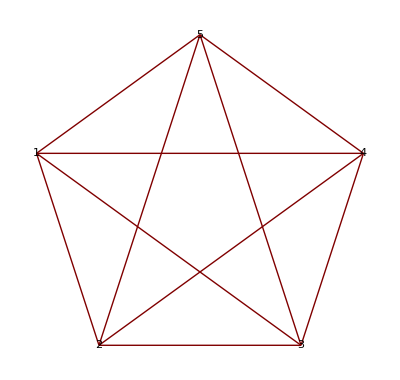
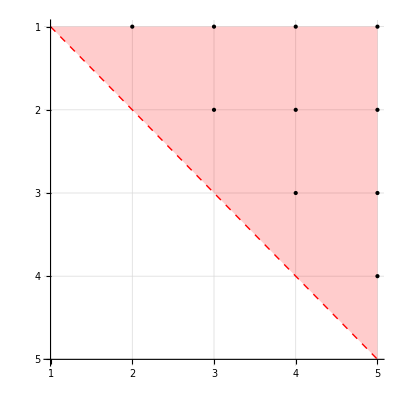

nFixedNeighs={∞,∞,∞,∞,0}

atomsToBeFixed={1,2,3,4}

Fixing: 1

atomOrder={1,0,0,0,0}

neighs={2,3,4,5}

nFixedNeighs={∞,∞,∞,∞,1}

atomsToBeFixed={2,3,4}

Fixing: 2

atomOrder={1,2,0,0,0}

neighs={1,3,4,5}

nFixedNeighs={∞,∞,∞,∞,2}

atomsToBeFixed={3,4}

Fixing: 3

atomOrder={1,2,3,0,0}

neighs={1,2,4,5}

nFixedNeighs={∞,∞,∞,∞,3}

atomsToBeFixed={4}

Fixing: 4

atomOrder={1,2,3,4,0}

neighs={1,2,3,5}

nFixedNeighs={∞,∞,∞,∞,4}

atomsToBeFixed={5}

Fixing: 5

atomOrder={1,2,3,4,5}

neighs={1,2,3,4}

{1,2,3,4,5}

```mathematica
G=Graph[{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,2<->5,3<->4,3<->5,4<->5}];
{GraphPlot[G,VertexLabeling->True],DGPlotAdjacencyMatrix[G,True]}
ii=DGOrdering[G,{1,2,3,4},True]
```

#### Harder Example: The initial ordering is not valid

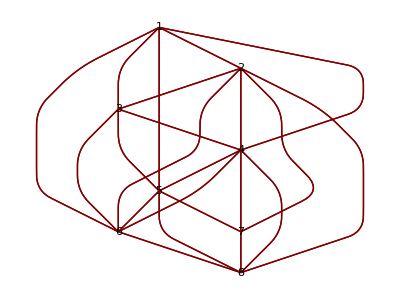
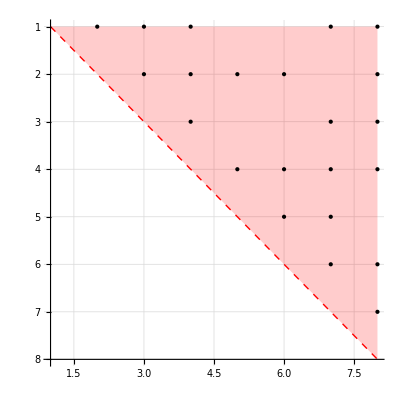

nFixedNeighs={∞,∞,∞,∞,0,0,0,0}

atomsToBeFixed={1,2,3,4}

Fixing: 1

atomOrder={1,0,0,0,0,0,0,0}

neighs={2,3,4,7,8}

nFixedNeighs={∞,∞,∞,∞,0,0,1,1}

atomsToBeFixed={2,3,4}

Fixing: 2

atomOrder={1,2,0,0,0,0,0,0}

neighs={1,3,4,8,5,6}

nFixedNeighs={∞,∞,∞,∞,1,1,1,2}

atomsToBeFixed={3,4}

Fixing: 3

atomOrder={1,2,3,0,0,0,0,0}

neighs={1,2,4,7,8}

nFixedNeighs={∞,∞,∞,∞,1,1,2,3}

atomsToBeFixed={4}

Fixing: 4

atomOrder={1,2,3,4,0,0,0,0}

neighs={1,2,3,7,8,5,6}

nFixedNeighs={∞,∞,∞,∞,2,2,3,4}

atomsToBeFixed={8}

Fixing: 8

atomOrder={1,2,3,4,0,0,0,5}

neighs={1,2,3,4,7,6}

nFixedNeighs={∞,∞,∞,∞,2,3,4,4}

atomsToBeFixed={7}

Fixing: 7

atomOrder={1,2,3,4,0,0,6,5}

neighs={1,3,4,8,5,6}

nFixedNeighs={∞,∞,∞,∞,3,4,4,5}

atomsToBeFixed={6}

Fixing: 6

atomOrder={1,2,3,4,0,7,6,5}

neighs={2,4,7,8,5}

nFixedNeighs={∞,∞,∞,∞,4,4,5,6}

atomsToBeFixed={5}

Fixing: 5

atomOrder={1,2,3,4,8,7,6,5}

neighs={2,4,7,6}

{1,2,3,4,8,7,6,5}

```mathematica
edges={1<->2,1<->3,1<->4,1<->7,1<->8,2<->3,2<->4,2<->5,2<->6,2<->8,3<->4,3<->7,3<->8,4<->6,4<->7,4<->8,4<->5,5<->6,5<->7,6<->7,6<->8,7<->8};
G=Graph[edges];
{LayeredGraphPlot[G,VertexLabeling->True],DGPlotAdjacencyMatrix[G,True]}
ii=DGOrdering[G,{1,2,3,4},True]
```

Intersection of spheres
DGIntersect3Spheres, DGIntersect4Spheres

```mathematica
ClearAll[DGIntersect3Spheres,DGIntersect4Spheres];
DGIntersect3Spheres[a_,ra_,b_,rb_,c_,rc_]:=
(* Gets the 2 solutions of {||x-a||=ra,||x-b||=rb,||x-c||=rc};
   Input;
   a,b,c: sphere centers;
   ra,rb,rc: respective sphere radius;
   Output;   
   x: the two intersections (x[[1]]: positive chirality and x[[2]]: negative chirality);
 *)
Module[{n,A,x,p,dp,u,v,w,du,dv,dw,dpu,AbsCos,error},
(* select the most perpendicular vertex angle (stability) *)
(*Print["a=",a,"  ra=",ra,"  b=",b,"  rb=",rb,"  c=",c,"  rc=",rc];*)
AbsCos[u_,v_]:=Dot[u,v]/(Norm[u]*Norm[v]);
{u,v,w,du,dv,dw}=MinimalBy[{
{AbsCos[b-a,c-a],{a,b,c,ra,rb,rc}},
{AbsCos[c-b,a-b],{b,c,a,rb,rc,ra}},
{AbsCos[a-c,b-c],{c,a,b,rc,ra,rb}}
},First][[1]][[2]];
(* normal to the plane (u,v,w) *)
n=Normalize[Cross[v-u,w-u]];
A={v-u,w-u,n};
x={(Dot[v,v]-Dot[u,u]-dv^2+du^2)/2,(Dot[w,w]-Dot[u,u]-dw^2+du^2)/2,Dot[n,u]};
p=LinearSolve[A,x];
(* select the factor with minimal canceling effect (stability) *)
{u,du}=MaximalBy[{
{Abs[(ra-Norm[p-a])/ra],{a,ra}},
{Abs[(rb-Norm[p-b])/rb],{b,rb}},
{Abs[(rc-Norm[p-c])/rc],{c,rc}}
},First][[1]][[2]];
dpu=Norm[p-u];
dp=N[Sqrt[(du+dpu)*(du-dpu)]];
(*dp=Re[dp];*)
x={p+dp*n,p-dp*n};
(*Print["a=",a,"  ra=",ra,"  b=",b,"  rb=",rb,"  c=",c,"  rc=",rc];
Print["p=",p,"  dp=",dp,"  x=",x];*)
(* calculating max relative errors of each solution *)
error=Table[Max[Abs[{(Norm[a-x[[i]]]-ra)/ra,(Norm[b-x[[i]]]-rb)/rb,(Norm[c-x[[i]]]-rc)/rc}]],{i,2}];
Return[{x,error}];
];

DGIntersect4Spheres[a_,ra_,b_,rb_,c_,rc_,d_,rd_]:=
Module[{x,error,errd1,errd2},
{x,error}=DGIntersect3Spheres[a,ra,b,rb,c,rc];
errd1=Abs[N[Norm[x[[1]]-d]]-rd];
errd2=Abs[N[Norm[x[[2]]-d]]-rd];
If[errd1<errd2,
x=x[[1]];
error=Max[error[[1]],errd1],
x=x[[2]];
error=Max[error[[2]],errd2]
];
Return[{x,error}]
];
```

DGBuildUpSolver
DGBuildUpInitX, DGBuildUpSetX, DGBuildUpSolver

### Source Code

```mathematica
ClearAll[
DGBuildUpInitX,
DGBuildUpSetX,
DGBuildUpSolver
]

DGBuildUpInitX[G_,basis_]:=Module[
{i1,i2,i3,i4,d12,d13,d14,d23,d24,d34,A,X,XBP,workBP,X21,X31,X32,X41,X42,error},
{i1,i2,i3,i4}=basis;
{d12,d13,d14,d23,d24,d34}=DGEdgeWeight[G,{i1<->i2,i1<->i3,i1<->i4,i2<->i3,i2<->i4,i3<->i4}];
(* set the position of the four atoms in the basis *)
X=Table[{0,0,0},{ii,Length[VertexList[G]]}];
X[[i2]][[1]]=d12;
X21=X[[i2]][[1]];
X[[i3]][[1]]=(d13^2-d23^2+X21^2)/(2*X21);
X31=X[[i3]][[1]];
X[[i3]][[2]]=Sqrt[d13^2-X31^2];
(*Print[" - - "];
Print[" > > X[[i1]] = ",X[[i1]],", d14 = ",d14, ", X[[i2]] = ",X[[i2]],", d24 = ",d24, ", X[[i3]] = ",X[[i3]], "d34 = ",d34];
Print[" - - "];*)
{X[[i4]],error}=DGIntersect3Spheres[X[[i1]],d14,X[[i2]],d24,X[[i3]],d34][[1]];
Return[X];
];

DGBuildUpSetX[G_,X_,nodes_,ii_]:=Module[
{jj,kk,neighs,basis,x,i1,i2,i3,i4,d1,d2,d3,d4,error},
kk=nodes[[ii]];
neighs=Intersection[AdjacencyList[G,kk],nodes[[1;;(ii-1)]]];
If[Length[neighs]<4,Throw["InvalidOrder: There is not enough neighs to set a basis"]];
basis=Subsets[neighs,{4}];
For[jj=1,jj≤Length[basis],jj++,
{i1,i2,i3,i4}=basis[[jj]];
{d1,d2,d3,d4}=DGEdgeWeight[G,{i1<->kk,i2<->kk,i3<->kk,i4<->kk}];
{x,error}=DGIntersect4Spheres[X[[i1]],d1,X[[i2]],d2,X[[i3]],d3,X[[i4]],d4];
If[error<10^(-3),Break];
];
If[error>10^(-3),Throw["InvalidSolution: A precise solution could not be found."]];
Return[x]
];

DGBuildUpSolver[G_,nodes_]:=Module[
{ii,X},
X=DGBuildUpInitX[G,nodes[[1;;4]]];
(* set remaining atoms *)
For[ii=5,ii≤Length[X],ii++,
X[[nodes[[ii]]]]=DGBuildUpSetX[G,X,nodes,ii]
];
Return[X]
];
```

### Example

#### Check DGBuildUpInitX

```mathematica
x={{0,0,0},{1,0,0},{0,1,0},{0,0,1},{1,1,0}};
edges={{1,2},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}};
P=DGProblem[x,edges];
DGPrintGraph[P["G"]]
basis={2,3,4,5};
x=DGBuildUpInitX[P["G"],basis];
DGPrintDistanceMatrix[x,edges]
```

| ii | jj | dij | lij | uij
1 | 1 | 2 | 1. | 1. | 1.
2 | 2 | 3 | 1.41421 | 1.41421 | 1.41421
3 | 2 | 4 | 1.41421 | 1.41421 | 1.41421
4 | 2 | 5 | 1. | 1. | 1.
5 | 3 | 4 | 1.41421 | 1.41421 | 1.41421
6 | 3 | 5 | 1. | 1. | 1.
7 | 4 | 5 | 1.73205 | 1.73205 | 1.73205

| ii | jj | dij
1 | 1 | 2 | 0.
2 | 2 | 3 | 1.41421
3 | 2 | 4 | 1.41421
4 | 2 | 5 | 1.
5 | 3 | 4 | 1.41421
6 | 3 | 5 | 1.
7 | 4 | 5 | 1.73205

#### Check DGBuildUpSolver

```mathematica
x={{0,0,0},{1,0,0},{1,1,0},{1,1,1},{1,0,1}};
edges={{1,2},{1,3},{1,4},{2,3},{2,4},{3,4},{1,5},{2,5},{3,5},{4,5}};
P=DGProblem[x,edges];
nodes={1,2,3,5,4};
x=DGBuildUpSolver[P["G"],nodes];
DGPrintX[x]
DGRelativeResidue[P["G"],x,True];
```

| x | y | z
1 | 0 | 0 | 0
2 | 1. | 0 | 0
3 | 1. | 1. | 0
4 | 1. | 1. | 1.
5 | 1. | -2.22045×10^-16 | 1.

Solution Quality

Number of nodes      : 5

Number of edges      : 10

Relative error bounds: {0.,4.44089×10^-16}

Mean relative error  : 5.55112×10^-17

#### Solving an instance using BuilUpSolver method

```mathematica
x={{0,0,0},{1,0,0},{1,1,0},{1,1,1},{1,0,1}};
edges={{1,2},{1,3},{1,4},{2,3},{2,4},{3,4},{1,5},{2,5},{3,5},{4,5}};
P=DGProblem[x,edges];
(*P=DGRandomMDGP[20,0.0,5.0,0];*)
X=P["X"];
G=P["G"];
nodes=Table[ii,{ii,Length[VertexList[G]]}]
(*extra*)
Print["- - - - -  Dados do BuildUpSolver - - - - -"];
X=DGBuildUpSolver[G,nodes];
DGRelativeResidue[G,X,True];
Print["Solução : ", X];
DGPlot3DBackbone[X,.2,0.1]

Print["- - - - -  - - - - - - - - - - - - -"];
Print["- - - - - Dados do BPSolver - - - - -"];
{XBP,workBP}=DGBPSolver[G,nodes,False,True];
DGRelativeResidue[G,XBP["Points"][[1]],True];
Print["Solução 1: ", XBP["Points"][[1]]];
Print["Solução 2: ", XBP["Points"][[2]]];
GraphicsGrid[{{DGPlot3DBackbone[XBP["Points"][[1]],.2,0.1],DGPlot3DBackbone[XBP["Points"][[2]],.2,0.1]}}]
```

{1,2,3,4,5}

- - - - -  Dados do BuildUpSolver - - - - -

Solution Quality

Number of nodes      : 5

Number of edges      : 10

Relative error bounds: {0.,4.44089×10^-16}

Mean relative error  : 5.55112×10^-17

Solução : {{0,0,0},{1.,0,0},{1.,1.,0},{1.,1.,1.},{1.,-2.22045×10^-16,1.}}

-Graphics3D-

- - - - -  - - - - - - - - - - - - -

- - - - - Dados do BPSolver - - - - -

Set::shape: Lists {XBP,workBP} and DGBPSolver[,{1,2,3,4,5},False,True] are not the same shape.

Part::partd: Part specification Points⟦1⟧ is longer than depth of object.

Part::partd: Part specification Points⟦2⟧ is longer than depth of object.

Part::partd: Part specification Points⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Solution Quality

Number of nodes      : 0

Number of edges      : 10

Relative error bounds: {Min[Max[1. Max[0,1.-Norm[Points⟦1⟧-Points⟦2⟧]],1. Max[0,-1.+Norm[Points⟦1⟧-Points⟦2⟧]]],Max[0.707107 Max[0,1.41421-Norm[Points⟦1⟧-Points⟦3⟧]],0.707107 Max[0,-1.41421+Norm[Points⟦1⟧-Points⟦3⟧]]],Max[1. Max[0,1.-Norm[Points⟦2⟧-Points⟦3⟧]],1. Max[0,-1.+Norm[Points⟦2⟧-Points⟦3⟧]]],Max[0.57735 Max[0,1.73205-Norm[Points⟦1⟧-Points⟦4⟧]],0.57735 Max[0,-1.73205+Norm[Points⟦1⟧-Points⟦4⟧]]],Max[0.707107 Max[0,1.41421-Norm[Points⟦2⟧-Points⟦4⟧]],0.707107 Max[0,-1.41421+Norm[Points⟦2⟧-Points⟦4⟧]]],Max[1. Max[0,1.-Norm[Points⟦3⟧-Points⟦4⟧]],1. Max[0,-1.+Norm[Points⟦3⟧-Points⟦4⟧]]],Max[0.707107 Max[0,1.41421-Norm[Points⟦1⟧-Points⟦5⟧]],0.707107 Max[0,-1.41421+Norm[Points⟦1⟧-Points⟦5⟧]]],Max[1. Max[0,1.-Norm[Points⟦2⟧-Points⟦5⟧]],1. Max[0,-1.+Norm[Points⟦2⟧-Points⟦5⟧]]],Max[0.707107 Max[0,1.41421-Norm[Points⟦3⟧-Points⟦5⟧]],0.707107 Max[0,-1.41421+Norm[Points⟦3⟧-Points⟦5⟧]]],Max[1. Max[0,1.-Norm[Points⟦4⟧-Points⟦5⟧]],1. Max[0,-1.+Norm[Points⟦4⟧-Points⟦5⟧]]]],Max[1. Max[0,1.-Norm[Points⟦1⟧-Points⟦2⟧]],1. Max[0,-1.+Norm[Points⟦1⟧-Points⟦2⟧]],0.707107 Max[0,1.41421-Norm[Points⟦1⟧-Points⟦3⟧]],0.707107 Max[0,-1.41421+Norm[Points⟦1⟧-Points⟦3⟧]],1. Max[0,1.-Norm[Points⟦2⟧-Points⟦3⟧]],1. Max[0,-1.+Norm[Points⟦2⟧-Points⟦3⟧]],0.57735 Max[0,1.73205-Norm[Points⟦1⟧-Points⟦4⟧]],0.57735 Max[0,-1.73205+Norm[Points⟦1⟧-Points⟦4⟧]],0.707107 Max[0,1.41421-Norm[Points⟦2⟧-Points⟦4⟧]],0.707107 Max[0,-1.41421+Norm[Points⟦2⟧-Points⟦4⟧]],1. Max[0,1.-Norm[Points⟦3⟧-Points⟦4⟧]],1. Max[0,-1.+Norm[Points⟦3⟧-Points⟦4⟧]],0.707107 Max[0,1.41421-Norm[Points⟦1⟧-Points⟦5⟧]],0.707107 Max[0,-1.41421+Norm[Points⟦1⟧-Points⟦5⟧]],1. Max[0,1.-Norm[Points⟦2⟧-Points⟦5⟧]],1. Max[0,-1.+Norm[Points⟦2⟧-Points⟦5⟧]],0.707107 Max[0,1.41421-Norm[Points⟦3⟧-Points⟦5⟧]],0.707107 Max[0,-1.41421+Norm[Points⟦3⟧-Points⟦5⟧]],1. Max[0,1.-Norm[Points⟦4⟧-Points⟦5⟧]],1. Max[0,-1.+Norm[Points⟦4⟧-Points⟦5⟧]]]}

Mean relative error  : 1/10 (Max[1. Max[0,1.-Norm[Points⟦1⟧-Points⟦2⟧]],1. Max[0,-1.+Norm[Points⟦1⟧-Points⟦2⟧]]]+Max[0.707107 Max[0,1.41421-Norm[Points⟦1⟧-Points⟦3⟧]],0.707107 Max[0,-1.41421+Norm[Points⟦1⟧-Points⟦3⟧]]]+Max[1. Max[0,1.-Norm[Points⟦2⟧-Points⟦3⟧]],1. Max[0,-1.+Norm[Points⟦2⟧-Points⟦3⟧]]]+Max[0.57735 Max[0,1.73205-Norm[Points⟦1⟧-Points⟦4⟧]],0.57735 Max[0,-1.73205+Norm[Points⟦1⟧-Points⟦4⟧]]]+Max[0.707107 Max[0,1.41421-Norm[Points⟦2⟧-Points⟦4⟧]],0.707107 Max[0,-1.41421+Norm[Points⟦2⟧-Points⟦4⟧]]]+Max[1. Max[0,1.-Norm[Points⟦3⟧-Points⟦4⟧]],1. Max[0,-1.+Norm[Points⟦3⟧-Points⟦4⟧]]]+Max[0.707107 Max[0,1.41421-Norm[Points⟦1⟧-Points⟦5⟧]],0.707107 Max[0,-1.41421+Norm[Points⟦1⟧-Points⟦5⟧]]]+Max[1. Max[0,1.-Norm[Points⟦2⟧-Points⟦5⟧]],1. Max[0,-1.+Norm[Points⟦2⟧-Points⟦5⟧]]]+Max[0.707107 Max[0,1.41421-Norm[Points⟦3⟧-Points⟦5⟧]],0.707107 Max[0,-1.41421+Norm[Points⟦3⟧-Points⟦5⟧]]]+Max[1. Max[0,1.-Norm[Points⟦4⟧-Points⟦5⟧]],1. Max[0,-1.+Norm[Points⟦4⟧-Points⟦5⟧]]])

Solução 1: Points

Part::partw: Part 2 of XBP[Points] does not exist.

Solução 2: XBP[Points]⟦2⟧

Part::partd: Part specification Points⟦1⟧ is longer than depth of object.

Part::partd: Part specification Points⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 2 of XBP[Points] does not exist.

Part::partw: Part 3 of XBP[Points]⟦2⟧ does not exist.

-Graphics-

```mathematica
natoms=20;
P=DGRandomMDGP[natoms,0,5];
nodes=Table[ii,{ii,natoms}];
tElapsed=Timing[x=DGBuildUpSolver[P["G"],nodes]]
```

{0.967206,{{0,0,0},{1.526,0,0},{2.03376,1.43905,0},{3.55922,1.43924,0.0402386},{4.03297,0.793844,1.33936},{5.55781,0.735552,1.35077},{6.12052,2.15311,1.30019},{5.59613,2.86346,0.0555665},{4.08209,3.02204,0.161435},{3.57247,3.83485,-1.02529},{3.92924,3.11644,-2.32347},{3.29114,3.8483,-3.50071},{3.89416,5.24524,-3.6173},{3.57956,6.04116,-2.35389},{4.34412,5.44571,-1.1751},{5.84375,5.55149,-1.43701},{6.60873,4.98691,-0.243386},{6.29503,5.81582,0.998865},{7.00701,5.2114,2.2057},{8.51277,5.20856,1.95798}}}

Hold[Throw[InvalidOrder: There is not enough neighs to set a basis]]

{0.312002,{{0,0,0},{1.526,0,0},{2.03376,1.43905,0},{1.54918,2.14846,1.26119},{2.01768,3.60059,1.23875},{1.45755,4.29576,0.00114069},{1.85452,5.76906,0.0229642},{3.37555,5.88573,-0.0160281},{3.77148,7.35937,-0.033447},{3.06655,8.06089,-1.19087},{1.55576,7.96254,-0.999773},{1.16073,8.66758,0.294658},{1.75415,7.91678,1.48328},{3.27486,7.89015,1.35914},{3.81327,9.31721,1.40696},{3.39903,9.97241,2.72142},{4.07946,11.3325,2.84738},{3.83736,11.8938,4.24558},{4.46155,10.9632,5.28143},{4.13172,11.4692,6.68281}}}

{0.592804,{{0,0,0},{1.526,0,0},{2.03376,1.43905,0},{1.46828,2.17701,1.21009},{1.90449,1.46593,2.48789},{3.42819,1.3975,2.53603},{3.95027,0.786738,1.23869},{3.49064,1.63563,0.0568311},{4.09561,1.0834,-1.2307},{3.63791,-0.358775,-1.429},{2.11464,-0.401507,-1.50976},{1.64161,0.490592,-2.6539},{0.116567,0.544446,-2.65862},{-0.439848,-0.848867,-2.93747},{-1.96432,-0.789429,-2.97123},{-2.52649,-2.20679,-3.03219},{-2.09557,-2.9779,-1.78785},{-2.57076,-4.42394,-1.8967},{-2.27664,-5.15481,-0.589801},{-2.57296,-6.64184,-0.761836}}}

{1.59121,{{0,0,0},{1.526,0,0},{2.03376,1.43905,0},{1.48512,2.17106,1.22141},{1.82775,3.65468,1.12052},{1.39537,4.36384,2.40068},{-0.0534557,4.00333,2.71631},{-0.965723,4.57211,1.63329},{-2.4075,4.15949,1.91561},{-2.83976,4.71773,3.26846},{-1.74244,4.46158,4.29752},{-0.470441,5.19154,3.87579},{0.113205,4.51978,2.63613},{0.654879,3.14353,3.01189},{1.5973,3.27711,4.20465},{0.834728,3.85861,5.39167},{1.78155,4.00925,6.5789},{2.92417,4.94758,6.20124},{2.35938,6.32321,5.85869},{3.50587,7.27583,5.53196}}}

{2.66762,{{0,0,0},{1.526,0,0},{2.03376,1.43905,0},{1.51155,2.16174,1.23843},{0.0007042,2.34184,1.12191},{-0.499483,3.1983,2.28164},{0.156436,4.57459,2.21627},{1.64741,4.44108,2.51267},{2.29537,3.54292,1.46285},{3.75192,3.28931,1.84075},{4.42996,2.48307,0.736707},{3.67744,1.17164,0.530428},{2.2253,1.47087,0.16931},{1.43331,0.16713,0.128106},{-0.0297233,0.471338,-0.181174},{-0.539987,1.54133,0.779771},{-1.9957,1.86344,0.454449},{-2.8432,0.605149,0.61912},{-4.26246,0.881431,0.131218},{-4.2263,1.26342,-1.34576}}}

### Comparando o BuildUpSolver com o BPSolver

```mathematica
natoms=20;
P=DGRandomMDGP[natoms,0.0,5.0,0];
X=P["X"];
G=P["G"];
nodes=Table[ii,{ii,Length[VertexList[G]]}]
(*extra*)
Print["- - - - -  Dados do BuildUpSolver - - - - -"];
X=DGBuildUpSolver[G,nodes];
DGRelativeResidue[G,X,True];
Print["Solução : ", X];

Print["- - - - -  - - - - - - - - - - - - -"];
Print["- - - - - Dados do BPSolver - - - - -"];
{XBP,workBP}=DGBPSolver[G,nodes,False,True];
DGRelativeResidue[G,XBP["Points"][[1]],True];
Print["Solução 1: ", XBP["Points"][[1]]];
Print["Solução 2: ", XBP["Points"][[2]]];
GraphicsGrid[{{DGPlot3DBackbone[XBP["Points"][[1]],.2,0.1],DGPlot3DBackbone[XBP["Points"][[2]],.2,0.1]}}]
DGPlot3DBackbone[X,.2,0.1]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

- - - - -  Dados do BuildUpSolver - - - - -

Solution Quality

Number of nodes      : 20

Number of edges      : 109

Relative error bounds: {0.,8.16007×10^-13}

Mean relative error  : 2.19399×10^-14

Solução : {{0,0,0},{1.526,0,0},{2.03376,1.43905,0},{1.51371,2.16098,1.23977},{2.03385,1.4597,2.4913},{1.36751,2.06211,3.72491},{1.98083,1.45224,4.98212},{1.35813,2.09912,6.216},{1.66967,3.59298,6.21801},{1.10928,4.22682,7.48801},{1.73042,3.55328,8.70834},{1.67026,2.03805,8.53761},{2.45609,1.63574,7.2929},{2.50325,0.113806,7.19209},{3.42556,-0.290786,6.04565},{2.87543,0.259596,4.73298},{3.72414,-0.251996,3.57252},{3.67551,-1.77691,3.54152},{4.64096,-2.29421,2.47899},{6.06236,-1.86647,2.83303}}

- - - - -  - - - - - - - - - - - - -

- - - - - Dados do BPSolver - - - - -

Set::shape: Lists {XBP,workBP} and … are not the same shape.

Part::partd: Part specification Points⟦1⟧ is longer than depth of object.

Part::partd: Part specification Points⟦2⟧ is longer than depth of object.

Part::partd: Part specification Points⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Solution Quality

Number of nodes      : 0

Number of edges      : 109

Relative error bounds: {Min[Max[0.655308 Max[0,1.526-Norm[Points⟦1⟧-Points⟦2⟧]],0.655308 Max[0,-1.526+Norm[Points⟦1⟧-Points⟦2⟧]]],Max[0.401382 Max[0,2.49139-Norm[Points⟦1⟧-Points⟦3⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦1⟧-Points⟦3⟧]]],Max[0.655308 Max[0,1.526-Norm[Points⟦2⟧-Points⟦3⟧]],0.655308 Max[0,-1.526+Norm[Points⟦2⟧-Points⟦3⟧]]],Max[0.343034 Max[0,2.91516-Norm[Points⟦1⟧-Points⟦4⟧]],0.343034 Max[0,-2.91516+Norm[Points⟦1⟧-Points⟦4⟧]]],Max[0.401382 Max[0,2.49139-Norm[Points⟦2⟧-Points⟦4⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦2⟧-Points⟦4⟧]]],Max[0.655308 Max[0,1.526-Norm[Points⟦3⟧-Points⟦4⟧]],0.655308 Max[0,-1.526+Norm[Points⟦3⟧-Points⟦4⟧]]],Max[0.283139 Max[0,3.53184-Norm[Points⟦1⟧-Points⟦5⟧]],0.283139 Max[0,-3.53184+Norm[Points⟦1⟧-Points⟦5⟧]]],Max[0.341092 Max[0,2.93176-Norm[Points⟦2⟧-Points⟦5⟧]],0.341092 Max[0,-2.93176+Norm[Points⟦2⟧-Points⟦5⟧]]],Max[0.401382 Max[0,2.49139-Norm[Points⟦3⟧-Points⟦5⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦3⟧-Points⟦5⟧]]],Max[0.655308 Max[0,1.526-Norm[Points⟦4⟧-Points⟦5⟧]],0.655308 Max[0,-1.526+Norm[Points⟦4⟧-Points⟦5⟧]]],Max[0.223622 Max[0,4.47183-Norm[Points⟦1⟧-Points⟦6⟧]],0.223622 Max[0,-4.47183+Norm[Points⟦1⟧-Points⟦6⟧]]],Max[0.234711 Max[0,4.26055-Norm[Points⟦2⟧-Points⟦6⟧]],0.234711 Max[0,-4.26055+Norm[Points⟦2⟧-Points⟦6⟧]]],Max[0.260758 Max[0,3.83497-Norm[Points⟦3⟧-Points⟦6⟧]],0.260758 Max[0,-3.83497+Norm[Points⟦3⟧-Points⟦6⟧]]],Max[0.401382 Max[0,2.49139-Norm[Points⟦4⟧-Points⟦6⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦4⟧-Points⟦6⟧]]],Max[0.655308 Max[0,1.526-Norm[Points⟦5⟧-Points⟦6⟧]],0.655308 Max[0,-1.526+Norm[Points⟦5⟧-Points⟦6⟧]]],Max[0.200706 Max[0,4.98242-Norm[Points⟦3⟧-Points⟦7⟧]],0.200706 Max[0,-4.98242+Norm[Points⟦3⟧-Points⟦7⟧]]],Max[0.260593 Max[0,3.8374-Norm[Points⟦4⟧-Points⟦7⟧]],0.260593 Max[0,-3.8374+Norm[Points⟦4⟧-Points⟦7⟧]]],Max[0.401382 Max[0,2.49139-Norm[Points⟦5⟧-Points⟦7⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦5⟧-Points⟦7⟧]]],Max[0.655308 Max[0,1.526-Norm[Points⟦6⟧-Points⟦7⟧]],0.655308 Max[0,-1.526+Norm[Points⟦6⟧-Points⟦7⟧]]],Max[0.200842 Max[0,4.97904-Norm[Points⟦4⟧-Points⟦8⟧]],0.200842 Max[0,-4.97904+Norm[Points⟦4⟧-Points⟦8⟧]]],Max[0.260476 Max[0,3.83912-Norm[Points⟦5⟧-Points⟦8⟧]],0.260476 Max[0,-3.83912+Norm[Points⟦5⟧-Points⟦8⟧]]],Max[0.401382 Max[0,2.49139-Norm[Points⟦6⟧-Points⟦8⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦6⟧-Points⟦8⟧]]],Max[0.655308 Max[0,1.526-Norm[Points⟦7⟧-Points⟦8⟧]],0.655308 Max[0,-1.526+Norm[Points⟦7⟧-Points⟦8⟧]]],Max[0.232045 Max[0,4.30951-Norm[Points⟦5⟧-Points⟦9⟧]],0.232045 Max[0,-4.30951+Norm[Points⟦5⟧-Points⟦9⟧]]],Max[0.340001 Max[0,2.94117-Norm[Points⟦6⟧-Points⟦9⟧]],0.340001 Max[0,-2.94117+Norm[Points⟦6⟧-Points⟦9⟧]]],Max[0.401382 Max[0,2.49139-Norm[Points⟦7⟧-Points⟦9⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦7⟧-Points⟦9⟧]]],Max[0.655308 Max[0,1.526-Norm[Points⟦8⟧-Points⟦9⟧]],0.655308 Max[0,-1.526+Norm[Points⟦8⟧-Points⟦9⟧]]],Max[0.229939 Max[0,4.34898-Norm[Points⟦6⟧-Points⟦10⟧]],0.229939 Max[0,-4.34898+Norm[Points⟦6⟧-Points⟦10⟧]]],Max[0.260489 Max[0,3.83893-Norm[Points⟦7⟧-Points⟦10⟧]],0.260489 Max[0,-3.83893+Norm[Points⟦7⟧-Points⟦10⟧]]],Max[0.401382 Max[0,2.49139-Norm[Points⟦8⟧-Points⟦10⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦8⟧-Points⟦10⟧]]],Max[0.655308 Max[0,1.526-Norm[Points⟦9⟧-Points⟦10⟧]],0.655308 Max[0,-1.526+Norm[Points⟦9⟧-Points⟦10⟧]]],Max[0.233368 Max[0,4.28507-Norm[Points⟦7⟧-Points⟦11⟧]],0.233368 Max[0,-4.28507+Norm[Points⟦7⟧-Points⟦11⟧]]],Max[0.343707 Max[0,2.90946-Norm[Points⟦8⟧-Points⟦11⟧]],0.343707 Max[0,-2.90946+Norm[Points⟦8⟧-Points⟦11⟧]]],Max[0.401382 Max[0,2.49139-Norm[Points⟦9⟧-Points⟦11⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦9⟧-Points⟦11⟧]]],Max[0.655308 Max[0,1.526-Norm[Points⟦10⟧-Points⟦11⟧]],0.655308 Max[0,-1.526+Norm[Points⟦10⟧-Points⟦11⟧]]],Max[0.207371 Max[0,4.82227-Norm[Points⟦6⟧-Points⟦12⟧]],0.207371 Max[0,-4.82227+Norm[Points⟦6⟧-Points⟦12⟧]]],Max[0.276489 Max[0,3.61679-Norm[Points⟦7⟧-Points⟦12⟧]],0.276489 Max[0,-3.61679+Norm[Points⟦7⟧-Points⟦12⟧]]],Max[0.426751 Max[0,2.34329-Norm[Points⟦8⟧-Points⟦12⟧]],0.426751 Max[0,-2.34329+Norm[Points⟦8⟧-Points⟦12⟧]]],Max[0.358096 Max[0,2.79255-Norm[Points⟦9⟧-Points⟦12⟧]],0.358096 Max[0,-2.79255+Norm[Points⟦9⟧-Points⟦12⟧]]],Max[0.401382 Max[0,2.49139-Norm[Points⟦10⟧-Points⟦12⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦10⟧-Points⟦12⟧]]],Max[0.655308 Max[0,1.526-Norm[Points⟦11⟧-Points⟦12⟧]],0.655308 Max[0,-1.526+Norm[Points⟦11⟧-Points⟦12⟧]]],Max[0.207325 Max[0,4.82334-Norm[Points⟦5⟧-Points⟦13⟧]],0.207325 Max[0,-4.82334+Norm[Points⟦5⟧-Points⟦13⟧]]],Max[0.266337 Max[0,3.75465-Norm[Points⟦6⟧-Points⟦13⟧]],0.266337 Max[0,-3.75465+Norm[Points⟦6⟧-Points⟦13⟧]]],Max[0.422605 Max[0,2.36628-Norm[Points⟦7⟧-Points⟦13⟧]],0.422605 Max[0,-2.36628+Norm[Points⟦7⟧-Points⟦13⟧]]],Max[0.62258 Max[0,1.60622-Norm[Points⟦8⟧-Points⟦13⟧]],0.62258 Max[0,-1.60622+Norm[Points⟦8⟧-Points⟦13⟧]]],Max[0.422403 Max[0,2.36741-Norm[Points⟦9⟧-Points⟦13⟧]],0.422403 Max[0,-2.36741+Norm[Points⟦9⟧-Points⟦13⟧]]],Max[0.341681 Max[0,2.92671-Norm[Points⟦10⟧-Points⟦13⟧]],0.341681 Max[0,-2.92671+Norm[Points⟦10⟧-Points⟦13⟧]]],Max[0.401382 Max[0,2.49139-Norm[Points⟦11⟧-Points⟦13⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦11⟧-Points⟦13⟧]]],Max[0.655308 Max[0,1.526-Norm[Points⟦12⟧-Points⟦13⟧]],0.655308 Max[0,-1.526+Norm[Points⟦12⟧-Points⟦13⟧]]],Max[0.203577 Max[0,4.91214-Norm[Points⟦5⟧-Points⟦14⟧]],0.203577 Max[0,-4.91214+Norm[Points⟦5⟧-Points⟦14⟧]]],Max[0.241775 Max[0,4.13608-Norm[Points⟦6⟧-Points⟦14⟧]],0.241775 Max[0,-4.13608+Norm[Points⟦6⟧-Points⟦14⟧]]],Max[0.379368 Max[0,2.63596-Norm[Points⟦7⟧-Points⟦14⟧]],0.379368 Max[0,-2.63596+Norm[Points⟦7⟧-Points⟦14⟧]]],Max[0.401431 Max[0,2.49109-Norm[Points⟦8⟧-Points⟦14⟧]],0.401431 Max[0,-2.49109+Norm[Points⟦8⟧-Points⟦14⟧]]],Max[0.269696 Max[0,3.70788-Norm[Points⟦9⟧-Points⟦14⟧]],0.269696 Max[0,-3.70788+Norm[Points⟦9⟧-Points⟦14⟧]]],Max[0.229733 Max[0,4.35288-Norm[Points⟦10⟧-Points⟦14⟧]],0.229733 Max[0,-4.35288+Norm[Points⟦10⟧-Points⟦14⟧]]],Max[0.260588 Max[0,3.83748-Norm[Points⟦11⟧-Points⟦14⟧]],0.260588 Max[0,-3.83748+Norm[Points⟦11⟧-Points⟦14⟧]]],Max[0.401382 Max[0,2.49139-Norm[Points⟦12⟧-Points⟦14⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦12⟧-Points⟦14⟧]]],Max[0.655308 Max[0,1.526-Norm[Points⟦13⟧-Points⟦14⟧]],0.655308 Max[0,-1.526+Norm[Points⟦13⟧-Points⟦14⟧]]],Max[0.238133 Max[0,4.19934-Norm[Points⟦5⟧-Points⟦15⟧]],0.238133 Max[0,-4.19934+Norm[Points⟦5⟧-Points⟦15⟧]]],Max[0.256854 Max[0,3.89327-Norm[Points⟦6⟧-Points⟦15⟧]],0.256854 Max[0,-3.89327+Norm[Points⟦6⟧-Points⟦15⟧]]],Max[0.399792 Max[0,2.5013-Norm[Points⟦7⟧-Points⟦15⟧]],0.399792 Max[0,-2.5013+Norm[Points⟦7⟧-Points⟦15⟧]]],Max[0.315992 Max[0,3.16464-Norm[Points⟦8⟧-Points⟦15⟧]],0.315992 Max[0,-3.16464+Norm[Points⟦8⟧-Points⟦15⟧]]],Max[0.234426 Max[0,4.26574-Norm[Points⟦9⟧-Points⟦15⟧]],0.234426 Max[0,-4.26574+Norm[Points⟦9⟧-Points⟦15⟧]]],Max[0.201047 Max[0,4.97396-Norm[Points⟦11⟧-Points⟦15⟧]],0.201047 Max[0,-4.97396+Norm[Points⟦11⟧-Points⟦15⟧]]],Max[0.260692 Max[0,3.83594-Norm[Points⟦12⟧-Points⟦15⟧]],0.260692 Max[0,-3.83594+Norm[Points⟦12⟧-Points⟦15⟧]]],Max[0.401382 Max[0,2.49139-Norm[Points⟦13⟧-Points⟦15⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦13⟧-Points⟦15⟧]]],Max[0.655308 Max[0,1.526-Norm[Points⟦14⟧-Points⟦15⟧]],0.655308 Max[0,-1.526+Norm[Points⟦14⟧-Points⟦15⟧]]],Max[0.202904 Max[0,4.92843-Norm[Points⟦2⟧-Points⟦16⟧]],0.202904 Max[0,-4.92843+Norm[Points⟦2⟧-Points⟦16⟧]]],Max[0.202028 Max[0,4.94981-Norm[Points⟦3⟧-Points⟦16⟧]],0.202028 Max[0,-4.94981+Norm[Points⟦3⟧-Points⟦16⟧]]],Max[0.237879 Max[0,4.20381-Norm[Points⟦4⟧-Points⟦16⟧]],0.237879 Max[0,-4.20381+Norm[Points⟦4⟧-Points⟦16⟧]]],Max[0.373363 Max[0,2.67836-Norm[Points⟦5⟧-Points⟦16⟧]],0.373363 Max[0,-2.67836+Norm[Points⟦5⟧-Points⟦16⟧]]],Max[0.391059 Max[0,2.55716-Norm[Points⟦6⟧-Points⟦16⟧]],0.391059 Max[0,-2.55716+Norm[Points⟦6⟧-Points⟦16⟧]]],Max[0.661572 Max[0,1.51155-Norm[Points⟦7⟧-Points⟦16⟧]],0.661572 Max[0,-1.51155+Norm[Points⟦7⟧-Points⟦16⟧]]],Max[0.356113 Max[0,2.8081-Norm[Points⟦8⟧-Points⟦16⟧]],0.356113 Max[0,-2.8081+Norm[Points⟦8⟧-Points⟦16⟧]]],Max[0.260196 Max[0,3.84326-Norm[Points⟦9⟧-Points⟦16⟧]],0.260196 Max[0,-3.84326+Norm[Points⟦9⟧-Points⟦16⟧]]],Max[0.228871 Max[0,4.36928-Norm[Points⟦12⟧-Points⟦16⟧]],0.228871 Max[0,-4.36928+Norm[Points⟦12⟧-Points⟦16⟧]]],Max[0.340545 Max[0,2.93647-Norm[Points⟦13⟧-Points⟦16⟧]],0.340545 Max[0,-2.93647+Norm[Points⟦13⟧-Points⟦16⟧]]],Max[0.401382 Max[0,2.49139-Norm[Points⟦14⟧-Points⟦16⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦14⟧-Points⟦16⟧]]],Max[0.655308 Max[0,1.526-Norm[Points⟦15⟧-Points⟦16⟧]],0.655308 Max[0,-1.526+Norm[Points⟦15⟧-Points⟦16⟧]]],Max[0.237972 Max[0,4.20217-Norm[Points⟦2⟧-Points⟦17⟧]],0.237972 Max[0,-4.20217+Norm[Points⟦2⟧-Points⟦17⟧]]],Max[0.232621 Max[0,4.29883-Norm[Points⟦3⟧-Points⟦17⟧]],0.232621 Max[0,-4.29883+Norm[Points⟦3⟧-Points⟦17⟧]]],Max[0.248835 Max[0,4.01873-Norm[Points⟦4⟧-Points⟦17⟧]],0.248835 Max[0,-4.01873+Norm[Points⟦4⟧-Points⟦17⟧]]],Max[0.379158 Max[0,2.63742-Norm[Points⟦5⟧-Points⟦17⟧]],0.379158 Max[0,-2.63742+Norm[Points⟦5⟧-Points⟦17⟧]]],Max[0.302448 Max[0,3.30635-Norm[Points⟦6⟧-Points⟦17⟧]],0.302448 Max[0,-3.30635+Norm[Points⟦6⟧-Points⟦17⟧]]],Max[0.355099 Max[0,2.81611-Norm[Points⟦7⟧-Points⟦17⟧]],0.355099 Max[0,-2.81611+Norm[Points⟦7⟧-Points⟦17⟧]]],Max[0.234961 Max[0,4.25602-Norm[Points⟦8⟧-Points⟦17⟧]],0.234961 Max[0,-4.25602+Norm[Points⟦8⟧-Points⟦17⟧]]],Max[0.229339 Max[0,4.36036-Norm[Points⟦13⟧-Points⟦17⟧]],0.229339 Max[0,-4.36036+Norm[Points⟦13⟧-Points⟦17⟧]]],Max[0.260593 Max[0,3.8374-Norm[Points⟦14⟧-Points⟦17⟧]],0.260593 Max[0,-3.8374+Norm[Points⟦14⟧-Points⟦17⟧]]],Max[0.401382 Max[0,2.49139-Norm[Points⟦15⟧-Points⟦17⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦15⟧-Points⟦17⟧]]],Max[0.655308 Max[0,1.526-Norm[Points⟦16⟧-Points⟦17⟧]],0.655308 Max[0,-1.526+Norm[Points⟦16⟧-Points⟦17⟧]]],Max[0.221838 Max[0,4.50779-Norm[Points⟦2⟧-Points⟦18⟧]],0.221838 Max[0,-4.50779+Norm[Points⟦2⟧-Points⟦18⟧]]],Max[0.264687 Max[0,3.77804-Norm[Points⟦5⟧-Points⟦18⟧]],0.264687 Max[0,-3.77804+Norm[Points⟦5⟧-Points⟦18⟧]]],Max[0.223058 Max[0,4.48313-Norm[Points⟦6⟧-Points⟦18⟧]],0.223058 Max[0,-4.48313+Norm[Points⟦6⟧-Points⟦18⟧]]],Max[0.255034 Max[0,3.92105-Norm[Points⟦7⟧-Points⟦18⟧]],0.255034 Max[0,-3.92105+Norm[Points⟦7⟧-Points⟦18⟧]]],Max[0.233918 Max[0,4.275-Norm[Points⟦14⟧-Points⟦18⟧]],0.233918 Max[0,-4.275+Norm[Points⟦14⟧-Points⟦18⟧]]],Max[0.342159 Max[0,2.92262-Norm[Points⟦15⟧-Points⟦18⟧]],0.342159 Max[0,-2.92262+Norm[Points⟦15⟧-Points⟦18⟧]]],Max[0.401382 Max[0,2.49139-Norm[Points⟦16⟧-Points⟦18⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦16⟧-Points⟦18⟧]]],Max[0.655308 Max[0,1.526-Norm[Points⟦17⟧-Points⟦18⟧]],0.655308 Max[0,-1.526+Norm[Points⟦17⟧-Points⟦18⟧]]],Max[0.217639 Max[0,4.59476-Norm[Points⟦2⟧-Points⟦19⟧]],0.217639 Max[0,-4.59476+Norm[Points⟦2⟧-Points⟦19⟧]]],Max[0.218797 Max[0,4.57045-Norm[Points⟦5⟧-Points⟦19⟧]],0.218797 Max[0,-4.57045+Norm[Points⟦5⟧-Points⟦19⟧]]],Max[0.234326 Max[0,4.26755-Norm[Points⟦15⟧-Points⟦19⟧]],0.234326 Max[0,-4.26755+Norm[Points⟦15⟧-Points⟦19⟧]]],Max[0.260648 Max[0,3.8366-Norm[Points⟦16⟧-Points⟦19⟧]],0.260648 Max[0,-3.8366+Norm[Points⟦16⟧-Points⟦19⟧]]],Max[0.401382 Max[0,2.49139-Norm[Points⟦17⟧-Points⟦19⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦17⟧-Points⟦19⟧]]],Max[0.655308 Max[0,1.526-Norm[Points⟦18⟧-Points⟦19⟧]],0.655308 Max[0,-1.526+Norm[Points⟦18⟧-Points⟦19⟧]]],Max[0.224981 Max[0,4.44482-Norm[Points⟦15⟧-Points⟦20⟧]],0.224981 Max[0,-4.44482+Norm[Points⟦15⟧-Points⟦20⟧]]],Max[0.233849 Max[0,4.27626-Norm[Points⟦16⟧-Points⟦20⟧]],0.233849 Max[0,-4.27626+Norm[Points⟦16⟧-Points⟦20⟧]]],Max[0.340589 Max[0,2.93609-Norm[Points⟦17⟧-Points⟦20⟧]],0.340589 Max[0,-2.93609+Norm[Points⟦17⟧-Points⟦20⟧]]],Max[0.401382 Max[0,2.49139-Norm[Points⟦18⟧-Points⟦20⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦18⟧-Points⟦20⟧]]],Max[0.655308 Max[0,1.526-Norm[Points⟦19⟧-Points⟦20⟧]],0.655308 Max[0,-1.526+Norm[Points⟦19⟧-Points⟦20⟧]]]],Max[0.655308 Max[0,1.526-Norm[Points⟦1⟧-Points⟦2⟧]],0.655308 Max[0,-1.526+Norm[Points⟦1⟧-Points⟦2⟧]],0.401382 Max[0,2.49139-Norm[Points⟦1⟧-Points⟦3⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦1⟧-Points⟦3⟧]],0.655308 Max[0,1.526-Norm[Points⟦2⟧-Points⟦3⟧]],0.655308 Max[0,-1.526+Norm[Points⟦2⟧-Points⟦3⟧]],0.343034 Max[0,2.91516-Norm[Points⟦1⟧-Points⟦4⟧]],0.343034 Max[0,-2.91516+Norm[Points⟦1⟧-Points⟦4⟧]],0.401382 Max[0,2.49139-Norm[Points⟦2⟧-Points⟦4⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦2⟧-Points⟦4⟧]],0.655308 Max[0,1.526-Norm[Points⟦3⟧-Points⟦4⟧]],0.655308 Max[0,-1.526+Norm[Points⟦3⟧-Points⟦4⟧]],0.283139 Max[0,3.53184-Norm[Points⟦1⟧-Points⟦5⟧]],0.283139 Max[0,-3.53184+Norm[Points⟦1⟧-Points⟦5⟧]],0.341092 Max[0,2.93176-Norm[Points⟦2⟧-Points⟦5⟧]],0.341092 Max[0,-2.93176+Norm[Points⟦2⟧-Points⟦5⟧]],0.401382 Max[0,2.49139-Norm[Points⟦3⟧-Points⟦5⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦3⟧-Points⟦5⟧]],0.655308 Max[0,1.526-Norm[Points⟦4⟧-Points⟦5⟧]],0.655308 Max[0,-1.526+Norm[Points⟦4⟧-Points⟦5⟧]],0.223622 Max[0,4.47183-Norm[Points⟦1⟧-Points⟦6⟧]],0.223622 Max[0,-4.47183+Norm[Points⟦1⟧-Points⟦6⟧]],0.234711 Max[0,4.26055-Norm[Points⟦2⟧-Points⟦6⟧]],0.234711 Max[0,-4.26055+Norm[Points⟦2⟧-Points⟦6⟧]],0.260758 Max[0,3.83497-Norm[Points⟦3⟧-Points⟦6⟧]],0.260758 Max[0,-3.83497+Norm[Points⟦3⟧-Points⟦6⟧]],0.401382 Max[0,2.49139-Norm[Points⟦4⟧-Points⟦6⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦4⟧-Points⟦6⟧]],0.655308 Max[0,1.526-Norm[Points⟦5⟧-Points⟦6⟧]],0.655308 Max[0,-1.526+Norm[Points⟦5⟧-Points⟦6⟧]],0.200706 Max[0,4.98242-Norm[Points⟦3⟧-Points⟦7⟧]],0.200706 Max[0,-4.98242+Norm[Points⟦3⟧-Points⟦7⟧]],0.260593 Max[0,3.8374-Norm[Points⟦4⟧-Points⟦7⟧]],0.260593 Max[0,-3.8374+Norm[Points⟦4⟧-Points⟦7⟧]],0.401382 Max[0,2.49139-Norm[Points⟦5⟧-Points⟦7⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦5⟧-Points⟦7⟧]],0.655308 Max[0,1.526-Norm[Points⟦6⟧-Points⟦7⟧]],0.655308 Max[0,-1.526+Norm[Points⟦6⟧-Points⟦7⟧]],0.200842 Max[0,4.97904-Norm[Points⟦4⟧-Points⟦8⟧]],0.200842 Max[0,-4.97904+Norm[Points⟦4⟧-Points⟦8⟧]],0.260476 Max[0,3.83912-Norm[Points⟦5⟧-Points⟦8⟧]],0.260476 Max[0,-3.83912+Norm[Points⟦5⟧-Points⟦8⟧]],0.401382 Max[0,2.49139-Norm[Points⟦6⟧-Points⟦8⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦6⟧-Points⟦8⟧]],0.655308 Max[0,1.526-Norm[Points⟦7⟧-Points⟦8⟧]],0.655308 Max[0,-1.526+Norm[Points⟦7⟧-Points⟦8⟧]],0.232045 Max[0,4.30951-Norm[Points⟦5⟧-Points⟦9⟧]],0.232045 Max[0,-4.30951+Norm[Points⟦5⟧-Points⟦9⟧]],0.340001 Max[0,2.94117-Norm[Points⟦6⟧-Points⟦9⟧]],0.340001 Max[0,-2.94117+Norm[Points⟦6⟧-Points⟦9⟧]],0.401382 Max[0,2.49139-Norm[Points⟦7⟧-Points⟦9⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦7⟧-Points⟦9⟧]],0.655308 Max[0,1.526-Norm[Points⟦8⟧-Points⟦9⟧]],0.655308 Max[0,-1.526+Norm[Points⟦8⟧-Points⟦9⟧]],0.229939 Max[0,4.34898-Norm[Points⟦6⟧-Points⟦10⟧]],0.229939 Max[0,-4.34898+Norm[Points⟦6⟧-Points⟦10⟧]],0.260489 Max[0,3.83893-Norm[Points⟦7⟧-Points⟦10⟧]],0.260489 Max[0,-3.83893+Norm[Points⟦7⟧-Points⟦10⟧]],0.401382 Max[0,2.49139-Norm[Points⟦8⟧-Points⟦10⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦8⟧-Points⟦10⟧]],0.655308 Max[0,1.526-Norm[Points⟦9⟧-Points⟦10⟧]],0.655308 Max[0,-1.526+Norm[Points⟦9⟧-Points⟦10⟧]],0.233368 Max[0,4.28507-Norm[Points⟦7⟧-Points⟦11⟧]],0.233368 Max[0,-4.28507+Norm[Points⟦7⟧-Points⟦11⟧]],0.343707 Max[0,2.90946-Norm[Points⟦8⟧-Points⟦11⟧]],0.343707 Max[0,-2.90946+Norm[Points⟦8⟧-Points⟦11⟧]],0.401382 Max[0,2.49139-Norm[Points⟦9⟧-Points⟦11⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦9⟧-Points⟦11⟧]],0.655308 Max[0,1.526-Norm[Points⟦10⟧-Points⟦11⟧]],0.655308 Max[0,-1.526+Norm[Points⟦10⟧-Points⟦11⟧]],0.207371 Max[0,4.82227-Norm[Points⟦6⟧-Points⟦12⟧]],0.207371 Max[0,-4.82227+Norm[Points⟦6⟧-Points⟦12⟧]],0.276489 Max[0,3.61679-Norm[Points⟦7⟧-Points⟦12⟧]],0.276489 Max[0,-3.61679+Norm[Points⟦7⟧-Points⟦12⟧]],0.426751 Max[0,2.34329-Norm[Points⟦8⟧-Points⟦12⟧]],0.426751 Max[0,-2.34329+Norm[Points⟦8⟧-Points⟦12⟧]],0.358096 Max[0,2.79255-Norm[Points⟦9⟧-Points⟦12⟧]],0.358096 Max[0,-2.79255+Norm[Points⟦9⟧-Points⟦12⟧]],0.401382 Max[0,2.49139-Norm[Points⟦10⟧-Points⟦12⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦10⟧-Points⟦12⟧]],0.655308 Max[0,1.526-Norm[Points⟦11⟧-Points⟦12⟧]],0.655308 Max[0,-1.526+Norm[Points⟦11⟧-Points⟦12⟧]],0.207325 Max[0,4.82334-Norm[Points⟦5⟧-Points⟦13⟧]],0.207325 Max[0,-4.82334+Norm[Points⟦5⟧-Points⟦13⟧]],0.266337 Max[0,3.75465-Norm[Points⟦6⟧-Points⟦13⟧]],0.266337 Max[0,-3.75465+Norm[Points⟦6⟧-Points⟦13⟧]],0.422605 Max[0,2.36628-Norm[Points⟦7⟧-Points⟦13⟧]],0.422605 Max[0,-2.36628+Norm[Points⟦7⟧-Points⟦13⟧]],0.62258 Max[0,1.60622-Norm[Points⟦8⟧-Points⟦13⟧]],0.62258 Max[0,-1.60622+Norm[Points⟦8⟧-Points⟦13⟧]],0.422403 Max[0,2.36741-Norm[Points⟦9⟧-Points⟦13⟧]],0.422403 Max[0,-2.36741+Norm[Points⟦9⟧-Points⟦13⟧]],0.341681 Max[0,2.92671-Norm[Points⟦10⟧-Points⟦13⟧]],0.341681 Max[0,-2.92671+Norm[Points⟦10⟧-Points⟦13⟧]],0.401382 Max[0,2.49139-Norm[Points⟦11⟧-Points⟦13⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦11⟧-Points⟦13⟧]],0.655308 Max[0,1.526-Norm[Points⟦12⟧-Points⟦13⟧]],0.655308 Max[0,-1.526+Norm[Points⟦12⟧-Points⟦13⟧]],0.203577 Max[0,4.91214-Norm[Points⟦5⟧-Points⟦14⟧]],0.203577 Max[0,-4.91214+Norm[Points⟦5⟧-Points⟦14⟧]],0.241775 Max[0,4.13608-Norm[Points⟦6⟧-Points⟦14⟧]],0.241775 Max[0,-4.13608+Norm[Points⟦6⟧-Points⟦14⟧]],0.379368 Max[0,2.63596-Norm[Points⟦7⟧-Points⟦14⟧]],0.379368 Max[0,-2.63596+Norm[Points⟦7⟧-Points⟦14⟧]],0.401431 Max[0,2.49109-Norm[Points⟦8⟧-Points⟦14⟧]],0.401431 Max[0,-2.49109+Norm[Points⟦8⟧-Points⟦14⟧]],0.269696 Max[0,3.70788-Norm[Points⟦9⟧-Points⟦14⟧]],0.269696 Max[0,-3.70788+Norm[Points⟦9⟧-Points⟦14⟧]],0.229733 Max[0,4.35288-Norm[Points⟦10⟧-Points⟦14⟧]],0.229733 Max[0,-4.35288+Norm[Points⟦10⟧-Points⟦14⟧]],0.260588 Max[0,3.83748-Norm[Points⟦11⟧-Points⟦14⟧]],0.260588 Max[0,-3.83748+Norm[Points⟦11⟧-Points⟦14⟧]],0.401382 Max[0,2.49139-Norm[Points⟦12⟧-Points⟦14⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦12⟧-Points⟦14⟧]],0.655308 Max[0,1.526-Norm[Points⟦13⟧-Points⟦14⟧]],0.655308 Max[0,-1.526+Norm[Points⟦13⟧-Points⟦14⟧]],0.238133 Max[0,4.19934-Norm[Points⟦5⟧-Points⟦15⟧]],0.238133 Max[0,-4.19934+Norm[Points⟦5⟧-Points⟦15⟧]],0.256854 Max[0,3.89327-Norm[Points⟦6⟧-Points⟦15⟧]],0.256854 Max[0,-3.89327+Norm[Points⟦6⟧-Points⟦15⟧]],0.399792 Max[0,2.5013-Norm[Points⟦7⟧-Points⟦15⟧]],0.399792 Max[0,-2.5013+Norm[Points⟦7⟧-Points⟦15⟧]],0.315992 Max[0,3.16464-Norm[Points⟦8⟧-Points⟦15⟧]],0.315992 Max[0,-3.16464+Norm[Points⟦8⟧-Points⟦15⟧]],0.234426 Max[0,4.26574-Norm[Points⟦9⟧-Points⟦15⟧]],0.234426 Max[0,-4.26574+Norm[Points⟦9⟧-Points⟦15⟧]],0.201047 Max[0,4.97396-Norm[Points⟦11⟧-Points⟦15⟧]],0.201047 Max[0,-4.97396+Norm[Points⟦11⟧-Points⟦15⟧]],0.260692 Max[0,3.83594-Norm[Points⟦12⟧-Points⟦15⟧]],0.260692 Max[0,-3.83594+Norm[Points⟦12⟧-Points⟦15⟧]],0.401382 Max[0,2.49139-Norm[Points⟦13⟧-Points⟦15⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦13⟧-Points⟦15⟧]],0.655308 Max[0,1.526-Norm[Points⟦14⟧-Points⟦15⟧]],0.655308 Max[0,-1.526+Norm[Points⟦14⟧-Points⟦15⟧]],0.202904 Max[0,4.92843-Norm[Points⟦2⟧-Points⟦16⟧]],0.202904 Max[0,-4.92843+Norm[Points⟦2⟧-Points⟦16⟧]],0.202028 Max[0,4.94981-Norm[Points⟦3⟧-Points⟦16⟧]],0.202028 Max[0,-4.94981+Norm[Points⟦3⟧-Points⟦16⟧]],0.237879 Max[0,4.20381-Norm[Points⟦4⟧-Points⟦16⟧]],0.237879 Max[0,-4.20381+Norm[Points⟦4⟧-Points⟦16⟧]],0.373363 Max[0,2.67836-Norm[Points⟦5⟧-Points⟦16⟧]],0.373363 Max[0,-2.67836+Norm[Points⟦5⟧-Points⟦16⟧]],0.391059 Max[0,2.55716-Norm[Points⟦6⟧-Points⟦16⟧]],0.391059 Max[0,-2.55716+Norm[Points⟦6⟧-Points⟦16⟧]],0.661572 Max[0,1.51155-Norm[Points⟦7⟧-Points⟦16⟧]],0.661572 Max[0,-1.51155+Norm[Points⟦7⟧-Points⟦16⟧]],0.356113 Max[0,2.8081-Norm[Points⟦8⟧-Points⟦16⟧]],0.356113 Max[0,-2.8081+Norm[Points⟦8⟧-Points⟦16⟧]],0.260196 Max[0,3.84326-Norm[Points⟦9⟧-Points⟦16⟧]],0.260196 Max[0,-3.84326+Norm[Points⟦9⟧-Points⟦16⟧]],0.228871 Max[0,4.36928-Norm[Points⟦12⟧-Points⟦16⟧]],0.228871 Max[0,-4.36928+Norm[Points⟦12⟧-Points⟦16⟧]],0.340545 Max[0,2.93647-Norm[Points⟦13⟧-Points⟦16⟧]],0.340545 Max[0,-2.93647+Norm[Points⟦13⟧-Points⟦16⟧]],0.401382 Max[0,2.49139-Norm[Points⟦14⟧-Points⟦16⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦14⟧-Points⟦16⟧]],0.655308 Max[0,1.526-Norm[Points⟦15⟧-Points⟦16⟧]],0.655308 Max[0,-1.526+Norm[Points⟦15⟧-Points⟦16⟧]],0.237972 Max[0,4.20217-Norm[Points⟦2⟧-Points⟦17⟧]],0.237972 Max[0,-4.20217+Norm[Points⟦2⟧-Points⟦17⟧]],0.232621 Max[0,4.29883-Norm[Points⟦3⟧-Points⟦17⟧]],0.232621 Max[0,-4.29883+Norm[Points⟦3⟧-Points⟦17⟧]],0.248835 Max[0,4.01873-Norm[Points⟦4⟧-Points⟦17⟧]],0.248835 Max[0,-4.01873+Norm[Points⟦4⟧-Points⟦17⟧]],0.379158 Max[0,2.63742-Norm[Points⟦5⟧-Points⟦17⟧]],0.379158 Max[0,-2.63742+Norm[Points⟦5⟧-Points⟦17⟧]],0.302448 Max[0,3.30635-Norm[Points⟦6⟧-Points⟦17⟧]],0.302448 Max[0,-3.30635+Norm[Points⟦6⟧-Points⟦17⟧]],0.355099 Max[0,2.81611-Norm[Points⟦7⟧-Points⟦17⟧]],0.355099 Max[0,-2.81611+Norm[Points⟦7⟧-Points⟦17⟧]],0.234961 Max[0,4.25602-Norm[Points⟦8⟧-Points⟦17⟧]],0.234961 Max[0,-4.25602+Norm[Points⟦8⟧-Points⟦17⟧]],0.229339 Max[0,4.36036-Norm[Points⟦13⟧-Points⟦17⟧]],0.229339 Max[0,-4.36036+Norm[Points⟦13⟧-Points⟦17⟧]],0.260593 Max[0,3.8374-Norm[Points⟦14⟧-Points⟦17⟧]],0.260593 Max[0,-3.8374+Norm[Points⟦14⟧-Points⟦17⟧]],0.401382 Max[0,2.49139-Norm[Points⟦15⟧-Points⟦17⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦15⟧-Points⟦17⟧]],0.655308 Max[0,1.526-Norm[Points⟦16⟧-Points⟦17⟧]],0.655308 Max[0,-1.526+Norm[Points⟦16⟧-Points⟦17⟧]],0.221838 Max[0,4.50779-Norm[Points⟦2⟧-Points⟦18⟧]],0.221838 Max[0,-4.50779+Norm[Points⟦2⟧-Points⟦18⟧]],0.264687 Max[0,3.77804-Norm[Points⟦5⟧-Points⟦18⟧]],0.264687 Max[0,-3.77804+Norm[Points⟦5⟧-Points⟦18⟧]],0.223058 Max[0,4.48313-Norm[Points⟦6⟧-Points⟦18⟧]],0.223058 Max[0,-4.48313+Norm[Points⟦6⟧-Points⟦18⟧]],0.255034 Max[0,3.92105-Norm[Points⟦7⟧-Points⟦18⟧]],0.255034 Max[0,-3.92105+Norm[Points⟦7⟧-Points⟦18⟧]],0.233918 Max[0,4.275-Norm[Points⟦14⟧-Points⟦18⟧]],0.233918 Max[0,-4.275+Norm[Points⟦14⟧-Points⟦18⟧]],0.342159 Max[0,2.92262-Norm[Points⟦15⟧-Points⟦18⟧]],0.342159 Max[0,-2.92262+Norm[Points⟦15⟧-Points⟦18⟧]],0.401382 Max[0,2.49139-Norm[Points⟦16⟧-Points⟦18⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦16⟧-Points⟦18⟧]],0.655308 Max[0,1.526-Norm[Points⟦17⟧-Points⟦18⟧]],0.655308 Max[0,-1.526+Norm[Points⟦17⟧-Points⟦18⟧]],0.217639 Max[0,4.59476-Norm[Points⟦2⟧-Points⟦19⟧]],0.217639 Max[0,-4.59476+Norm[Points⟦2⟧-Points⟦19⟧]],0.218797 Max[0,4.57045-Norm[Points⟦5⟧-Points⟦19⟧]],0.218797 Max[0,-4.57045+Norm[Points⟦5⟧-Points⟦19⟧]],0.234326 Max[0,4.26755-Norm[Points⟦15⟧-Points⟦19⟧]],0.234326 Max[0,-4.26755+Norm[Points⟦15⟧-Points⟦19⟧]],0.260648 Max[0,3.8366-Norm[Points⟦16⟧-Points⟦19⟧]],0.260648 Max[0,-3.8366+Norm[Points⟦16⟧-Points⟦19⟧]],0.401382 Max[0,2.49139-Norm[Points⟦17⟧-Points⟦19⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦17⟧-Points⟦19⟧]],0.655308 Max[0,1.526-Norm[Points⟦18⟧-Points⟦19⟧]],0.655308 Max[0,-1.526+Norm[Points⟦18⟧-Points⟦19⟧]],0.224981 Max[0,4.44482-Norm[Points⟦15⟧-Points⟦20⟧]],0.224981 Max[0,-4.44482+Norm[Points⟦15⟧-Points⟦20⟧]],0.233849 Max[0,4.27626-Norm[Points⟦16⟧-Points⟦20⟧]],0.233849 Max[0,-4.27626+Norm[Points⟦16⟧-Points⟦20⟧]],0.340589 Max[0,2.93609-Norm[Points⟦17⟧-Points⟦20⟧]],0.340589 Max[0,-2.93609+Norm[Points⟦17⟧-Points⟦20⟧]],0.401382 Max[0,2.49139-Norm[Points⟦18⟧-Points⟦20⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦18⟧-Points⟦20⟧]],0.655308 Max[0,1.526-Norm[Points⟦19⟧-Points⟦20⟧]],0.655308 Max[0,-1.526+Norm[Points⟦19⟧-Points⟦20⟧]]]}

Mean relative error  : 1/109 (Max[0.655308 Max[0,1.526-Norm[Points⟦1⟧-Points⟦2⟧]],0.655308 Max[0,-1.526+Norm[Points⟦1⟧-Points⟦2⟧]]]+Max[0.401382 Max[0,2.49139-Norm[Points⟦1⟧-Points⟦3⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦1⟧-Points⟦3⟧]]]+Max[0.655308 Max[0,1.526-Norm[Points⟦2⟧-Points⟦3⟧]],0.655308 Max[0,-1.526+Norm[Points⟦2⟧-Points⟦3⟧]]]+Max[0.343034 Max[0,2.91516-Norm[Points⟦1⟧-Points⟦4⟧]],0.343034 Max[0,-2.91516+Norm[Points⟦1⟧-Points⟦4⟧]]]+Max[0.401382 Max[0,2.49139-Norm[Points⟦2⟧-Points⟦4⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦2⟧-Points⟦4⟧]]]+Max[0.655308 Max[0,1.526-Norm[Points⟦3⟧-Points⟦4⟧]],0.655308 Max[0,-1.526+Norm[Points⟦3⟧-Points⟦4⟧]]]+Max[0.283139 Max[0,3.53184-Norm[Points⟦1⟧-Points⟦5⟧]],0.283139 Max[0,-3.53184+Norm[Points⟦1⟧-Points⟦5⟧]]]+Max[0.341092 Max[0,2.93176-Norm[Points⟦2⟧-Points⟦5⟧]],0.341092 Max[0,-2.93176+Norm[Points⟦2⟧-Points⟦5⟧]]]+Max[0.401382 Max[0,2.49139-Norm[Points⟦3⟧-Points⟦5⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦3⟧-Points⟦5⟧]]]+Max[0.655308 Max[0,1.526-Norm[Points⟦4⟧-Points⟦5⟧]],0.655308 Max[0,-1.526+Norm[Points⟦4⟧-Points⟦5⟧]]]+Max[0.223622 Max[0,4.47183-Norm[Points⟦1⟧-Points⟦6⟧]],0.223622 Max[0,-4.47183+Norm[Points⟦1⟧-Points⟦6⟧]]]+Max[0.234711 Max[0,4.26055-Norm[Points⟦2⟧-Points⟦6⟧]],0.234711 Max[0,-4.26055+Norm[Points⟦2⟧-Points⟦6⟧]]]+Max[0.260758 Max[0,3.83497-Norm[Points⟦3⟧-Points⟦6⟧]],0.260758 Max[0,-3.83497+Norm[Points⟦3⟧-Points⟦6⟧]]]+Max[0.401382 Max[0,2.49139-Norm[Points⟦4⟧-Points⟦6⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦4⟧-Points⟦6⟧]]]+Max[0.655308 Max[0,1.526-Norm[Points⟦5⟧-Points⟦6⟧]],0.655308 Max[0,-1.526+Norm[Points⟦5⟧-Points⟦6⟧]]]+Max[0.200706 Max[0,4.98242-Norm[Points⟦3⟧-Points⟦7⟧]],0.200706 Max[0,-4.98242+Norm[Points⟦3⟧-Points⟦7⟧]]]+Max[0.260593 Max[0,3.8374-Norm[Points⟦4⟧-Points⟦7⟧]],0.260593 Max[0,-3.8374+Norm[Points⟦4⟧-Points⟦7⟧]]]+Max[0.401382 Max[0,2.49139-Norm[Points⟦5⟧-Points⟦7⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦5⟧-Points⟦7⟧]]]+Max[0.655308 Max[0,1.526-Norm[Points⟦6⟧-Points⟦7⟧]],0.655308 Max[0,-1.526+Norm[Points⟦6⟧-Points⟦7⟧]]]+Max[0.200842 Max[0,4.97904-Norm[Points⟦4⟧-Points⟦8⟧]],0.200842 Max[0,-4.97904+Norm[Points⟦4⟧-Points⟦8⟧]]]+Max[0.260476 Max[0,3.83912-Norm[Points⟦5⟧-Points⟦8⟧]],0.260476 Max[0,-3.83912+Norm[Points⟦5⟧-Points⟦8⟧]]]+Max[0.401382 Max[0,2.49139-Norm[Points⟦6⟧-Points⟦8⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦6⟧-Points⟦8⟧]]]+Max[0.655308 Max[0,1.526-Norm[Points⟦7⟧-Points⟦8⟧]],0.655308 Max[0,-1.526+Norm[Points⟦7⟧-Points⟦8⟧]]]+Max[0.232045 Max[0,4.30951-Norm[Points⟦5⟧-Points⟦9⟧]],0.232045 Max[0,-4.30951+Norm[Points⟦5⟧-Points⟦9⟧]]]+Max[0.340001 Max[0,2.94117-Norm[Points⟦6⟧-Points⟦9⟧]],0.340001 Max[0,-2.94117+Norm[Points⟦6⟧-Points⟦9⟧]]]+Max[0.401382 Max[0,2.49139-Norm[Points⟦7⟧-Points⟦9⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦7⟧-Points⟦9⟧]]]+Max[0.655308 Max[0,1.526-Norm[Points⟦8⟧-Points⟦9⟧]],0.655308 Max[0,-1.526+Norm[Points⟦8⟧-Points⟦9⟧]]]+Max[0.229939 Max[0,4.34898-Norm[Points⟦6⟧-Points⟦10⟧]],0.229939 Max[0,-4.34898+Norm[Points⟦6⟧-Points⟦10⟧]]]+Max[0.260489 Max[0,3.83893-Norm[Points⟦7⟧-Points⟦10⟧]],0.260489 Max[0,-3.83893+Norm[Points⟦7⟧-Points⟦10⟧]]]+Max[0.401382 Max[0,2.49139-Norm[Points⟦8⟧-Points⟦10⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦8⟧-Points⟦10⟧]]]+Max[0.655308 Max[0,1.526-Norm[Points⟦9⟧-Points⟦10⟧]],0.655308 Max[0,-1.526+Norm[Points⟦9⟧-Points⟦10⟧]]]+Max[0.233368 Max[0,4.28507-Norm[Points⟦7⟧-Points⟦11⟧]],0.233368 Max[0,-4.28507+Norm[Points⟦7⟧-Points⟦11⟧]]]+Max[0.343707 Max[0,2.90946-Norm[Points⟦8⟧-Points⟦11⟧]],0.343707 Max[0,-2.90946+Norm[Points⟦8⟧-Points⟦11⟧]]]+Max[0.401382 Max[0,2.49139-Norm[Points⟦9⟧-Points⟦11⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦9⟧-Points⟦11⟧]]]+Max[0.655308 Max[0,1.526-Norm[Points⟦10⟧-Points⟦11⟧]],0.655308 Max[0,-1.526+Norm[Points⟦10⟧-Points⟦11⟧]]]+Max[0.207371 Max[0,4.82227-Norm[Points⟦6⟧-Points⟦12⟧]],0.207371 Max[0,-4.82227+Norm[Points⟦6⟧-Points⟦12⟧]]]+Max[0.276489 Max[0,3.61679-Norm[Points⟦7⟧-Points⟦12⟧]],0.276489 Max[0,-3.61679+Norm[Points⟦7⟧-Points⟦12⟧]]]+Max[0.426751 Max[0,2.34329-Norm[Points⟦8⟧-Points⟦12⟧]],0.426751 Max[0,-2.34329+Norm[Points⟦8⟧-Points⟦12⟧]]]+Max[0.358096 Max[0,2.79255-Norm[Points⟦9⟧-Points⟦12⟧]],0.358096 Max[0,-2.79255+Norm[Points⟦9⟧-Points⟦12⟧]]]+Max[0.401382 Max[0,2.49139-Norm[Points⟦10⟧-Points⟦12⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦10⟧-Points⟦12⟧]]]+Max[0.655308 Max[0,1.526-Norm[Points⟦11⟧-Points⟦12⟧]],0.655308 Max[0,-1.526+Norm[Points⟦11⟧-Points⟦12⟧]]]+Max[0.207325 Max[0,4.82334-Norm[Points⟦5⟧-Points⟦13⟧]],0.207325 Max[0,-4.82334+Norm[Points⟦5⟧-Points⟦13⟧]]]+Max[0.266337 Max[0,3.75465-Norm[Points⟦6⟧-Points⟦13⟧]],0.266337 Max[0,-3.75465+Norm[Points⟦6⟧-Points⟦13⟧]]]+Max[0.422605 Max[0,2.36628-Norm[Points⟦7⟧-Points⟦13⟧]],0.422605 Max[0,-2.36628+Norm[Points⟦7⟧-Points⟦13⟧]]]+Max[0.62258 Max[0,1.60622-Norm[Points⟦8⟧-Points⟦13⟧]],0.62258 Max[0,-1.60622+Norm[Points⟦8⟧-Points⟦13⟧]]]+Max[0.422403 Max[0,2.36741-Norm[Points⟦9⟧-Points⟦13⟧]],0.422403 Max[0,-2.36741+Norm[Points⟦9⟧-Points⟦13⟧]]]+Max[0.341681 Max[0,2.92671-Norm[Points⟦10⟧-Points⟦13⟧]],0.341681 Max[0,-2.92671+Norm[Points⟦10⟧-Points⟦13⟧]]]+Max[0.401382 Max[0,2.49139-Norm[Points⟦11⟧-Points⟦13⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦11⟧-Points⟦13⟧]]]+Max[0.655308 Max[0,1.526-Norm[Points⟦12⟧-Points⟦13⟧]],0.655308 Max[0,-1.526+Norm[Points⟦12⟧-Points⟦13⟧]]]+Max[0.203577 Max[0,4.91214-Norm[Points⟦5⟧-Points⟦14⟧]],0.203577 Max[0,-4.91214+Norm[Points⟦5⟧-Points⟦14⟧]]]+Max[0.241775 Max[0,4.13608-Norm[Points⟦6⟧-Points⟦14⟧]],0.241775 Max[0,-4.13608+Norm[Points⟦6⟧-Points⟦14⟧]]]+Max[0.379368 Max[0,2.63596-Norm[Points⟦7⟧-Points⟦14⟧]],0.379368 Max[0,-2.63596+Norm[Points⟦7⟧-Points⟦14⟧]]]+Max[0.401431 Max[0,2.49109-Norm[Points⟦8⟧-Points⟦14⟧]],0.401431 Max[0,-2.49109+Norm[Points⟦8⟧-Points⟦14⟧]]]+Max[0.269696 Max[0,3.70788-Norm[Points⟦9⟧-Points⟦14⟧]],0.269696 Max[0,-3.70788+Norm[Points⟦9⟧-Points⟦14⟧]]]+Max[0.229733 Max[0,4.35288-Norm[Points⟦10⟧-Points⟦14⟧]],0.229733 Max[0,-4.35288+Norm[Points⟦10⟧-Points⟦14⟧]]]+Max[0.260588 Max[0,3.83748-Norm[Points⟦11⟧-Points⟦14⟧]],0.260588 Max[0,-3.83748+Norm[Points⟦11⟧-Points⟦14⟧]]]+Max[0.401382 Max[0,2.49139-Norm[Points⟦12⟧-Points⟦14⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦12⟧-Points⟦14⟧]]]+Max[0.655308 Max[0,1.526-Norm[Points⟦13⟧-Points⟦14⟧]],0.655308 Max[0,-1.526+Norm[Points⟦13⟧-Points⟦14⟧]]]+Max[0.238133 Max[0,4.19934-Norm[Points⟦5⟧-Points⟦15⟧]],0.238133 Max[0,-4.19934+Norm[Points⟦5⟧-Points⟦15⟧]]]+Max[0.256854 Max[0,3.89327-Norm[Points⟦6⟧-Points⟦15⟧]],0.256854 Max[0,-3.89327+Norm[Points⟦6⟧-Points⟦15⟧]]]+Max[0.399792 Max[0,2.5013-Norm[Points⟦7⟧-Points⟦15⟧]],0.399792 Max[0,-2.5013+Norm[Points⟦7⟧-Points⟦15⟧]]]+Max[0.315992 Max[0,3.16464-Norm[Points⟦8⟧-Points⟦15⟧]],0.315992 Max[0,-3.16464+Norm[Points⟦8⟧-Points⟦15⟧]]]+Max[0.234426 Max[0,4.26574-Norm[Points⟦9⟧-Points⟦15⟧]],0.234426 Max[0,-4.26574+Norm[Points⟦9⟧-Points⟦15⟧]]]+Max[0.201047 Max[0,4.97396-Norm[Points⟦11⟧-Points⟦15⟧]],0.201047 Max[0,-4.97396+Norm[Points⟦11⟧-Points⟦15⟧]]]+Max[0.260692 Max[0,3.83594-Norm[Points⟦12⟧-Points⟦15⟧]],0.260692 Max[0,-3.83594+Norm[Points⟦12⟧-Points⟦15⟧]]]+Max[0.401382 Max[0,2.49139-Norm[Points⟦13⟧-Points⟦15⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦13⟧-Points⟦15⟧]]]+Max[0.655308 Max[0,1.526-Norm[Points⟦14⟧-Points⟦15⟧]],0.655308 Max[0,-1.526+Norm[Points⟦14⟧-Points⟦15⟧]]]+Max[0.202904 Max[0,4.92843-Norm[Points⟦2⟧-Points⟦16⟧]],0.202904 Max[0,-4.92843+Norm[Points⟦2⟧-Points⟦16⟧]]]+Max[0.202028 Max[0,4.94981-Norm[Points⟦3⟧-Points⟦16⟧]],0.202028 Max[0,-4.94981+Norm[Points⟦3⟧-Points⟦16⟧]]]+Max[0.237879 Max[0,4.20381-Norm[Points⟦4⟧-Points⟦16⟧]],0.237879 Max[0,-4.20381+Norm[Points⟦4⟧-Points⟦16⟧]]]+Max[0.373363 Max[0,2.67836-Norm[Points⟦5⟧-Points⟦16⟧]],0.373363 Max[0,-2.67836+Norm[Points⟦5⟧-Points⟦16⟧]]]+Max[0.391059 Max[0,2.55716-Norm[Points⟦6⟧-Points⟦16⟧]],0.391059 Max[0,-2.55716+Norm[Points⟦6⟧-Points⟦16⟧]]]+Max[0.661572 Max[0,1.51155-Norm[Points⟦7⟧-Points⟦16⟧]],0.661572 Max[0,-1.51155+Norm[Points⟦7⟧-Points⟦16⟧]]]+Max[0.356113 Max[0,2.8081-Norm[Points⟦8⟧-Points⟦16⟧]],0.356113 Max[0,-2.8081+Norm[Points⟦8⟧-Points⟦16⟧]]]+Max[0.260196 Max[0,3.84326-Norm[Points⟦9⟧-Points⟦16⟧]],0.260196 Max[0,-3.84326+Norm[Points⟦9⟧-Points⟦16⟧]]]+Max[0.228871 Max[0,4.36928-Norm[Points⟦12⟧-Points⟦16⟧]],0.228871 Max[0,-4.36928+Norm[Points⟦12⟧-Points⟦16⟧]]]+Max[0.340545 Max[0,2.93647-Norm[Points⟦13⟧-Points⟦16⟧]],0.340545 Max[0,-2.93647+Norm[Points⟦13⟧-Points⟦16⟧]]]+Max[0.401382 Max[0,2.49139-Norm[Points⟦14⟧-Points⟦16⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦14⟧-Points⟦16⟧]]]+Max[0.655308 Max[0,1.526-Norm[Points⟦15⟧-Points⟦16⟧]],0.655308 Max[0,-1.526+Norm[Points⟦15⟧-Points⟦16⟧]]]+Max[0.237972 Max[0,4.20217-Norm[Points⟦2⟧-Points⟦17⟧]],0.237972 Max[0,-4.20217+Norm[Points⟦2⟧-Points⟦17⟧]]]+Max[0.232621 Max[0,4.29883-Norm[Points⟦3⟧-Points⟦17⟧]],0.232621 Max[0,-4.29883+Norm[Points⟦3⟧-Points⟦17⟧]]]+Max[0.248835 Max[0,4.01873-Norm[Points⟦4⟧-Points⟦17⟧]],0.248835 Max[0,-4.01873+Norm[Points⟦4⟧-Points⟦17⟧]]]+Max[0.379158 Max[0,2.63742-Norm[Points⟦5⟧-Points⟦17⟧]],0.379158 Max[0,-2.63742+Norm[Points⟦5⟧-Points⟦17⟧]]]+Max[0.302448 Max[0,3.30635-Norm[Points⟦6⟧-Points⟦17⟧]],0.302448 Max[0,-3.30635+Norm[Points⟦6⟧-Points⟦17⟧]]]+Max[0.355099 Max[0,2.81611-Norm[Points⟦7⟧-Points⟦17⟧]],0.355099 Max[0,-2.81611+Norm[Points⟦7⟧-Points⟦17⟧]]]+Max[0.234961 Max[0,4.25602-Norm[Points⟦8⟧-Points⟦17⟧]],0.234961 Max[0,-4.25602+Norm[Points⟦8⟧-Points⟦17⟧]]]+Max[0.229339 Max[0,4.36036-Norm[Points⟦13⟧-Points⟦17⟧]],0.229339 Max[0,-4.36036+Norm[Points⟦13⟧-Points⟦17⟧]]]+Max[0.260593 Max[0,3.8374-Norm[Points⟦14⟧-Points⟦17⟧]],0.260593 Max[0,-3.8374+Norm[Points⟦14⟧-Points⟦17⟧]]]+Max[0.401382 Max[0,2.49139-Norm[Points⟦15⟧-Points⟦17⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦15⟧-Points⟦17⟧]]]+Max[0.655308 Max[0,1.526-Norm[Points⟦16⟧-Points⟦17⟧]],0.655308 Max[0,-1.526+Norm[Points⟦16⟧-Points⟦17⟧]]]+Max[0.221838 Max[0,4.50779-Norm[Points⟦2⟧-Points⟦18⟧]],0.221838 Max[0,-4.50779+Norm[Points⟦2⟧-Points⟦18⟧]]]+Max[0.264687 Max[0,3.77804-Norm[Points⟦5⟧-Points⟦18⟧]],0.264687 Max[0,-3.77804+Norm[Points⟦5⟧-Points⟦18⟧]]]+Max[0.223058 Max[0,4.48313-Norm[Points⟦6⟧-Points⟦18⟧]],0.223058 Max[0,-4.48313+Norm[Points⟦6⟧-Points⟦18⟧]]]+Max[0.255034 Max[0,3.92105-Norm[Points⟦7⟧-Points⟦18⟧]],0.255034 Max[0,-3.92105+Norm[Points⟦7⟧-Points⟦18⟧]]]+Max[0.233918 Max[0,4.275-Norm[Points⟦14⟧-Points⟦18⟧]],0.233918 Max[0,-4.275+Norm[Points⟦14⟧-Points⟦18⟧]]]+Max[0.342159 Max[0,2.92262-Norm[Points⟦15⟧-Points⟦18⟧]],0.342159 Max[0,-2.92262+Norm[Points⟦15⟧-Points⟦18⟧]]]+Max[0.401382 Max[0,2.49139-Norm[Points⟦16⟧-Points⟦18⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦16⟧-Points⟦18⟧]]]+Max[0.655308 Max[0,1.526-Norm[Points⟦17⟧-Points⟦18⟧]],0.655308 Max[0,-1.526+Norm[Points⟦17⟧-Points⟦18⟧]]]+Max[0.217639 Max[0,4.59476-Norm[Points⟦2⟧-Points⟦19⟧]],0.217639 Max[0,-4.59476+Norm[Points⟦2⟧-Points⟦19⟧]]]+Max[0.218797 Max[0,4.57045-Norm[Points⟦5⟧-Points⟦19⟧]],0.218797 Max[0,-4.57045+Norm[Points⟦5⟧-Points⟦19⟧]]]+Max[0.234326 Max[0,4.26755-Norm[Points⟦15⟧-Points⟦19⟧]],0.234326 Max[0,-4.26755+Norm[Points⟦15⟧-Points⟦19⟧]]]+Max[0.260648 Max[0,3.8366-Norm[Points⟦16⟧-Points⟦19⟧]],0.260648 Max[0,-3.8366+Norm[Points⟦16⟧-Points⟦19⟧]]]+Max[0.401382 Max[0,2.49139-Norm[Points⟦17⟧-Points⟦19⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦17⟧-Points⟦19⟧]]]+Max[0.655308 Max[0,1.526-Norm[Points⟦18⟧-Points⟦19⟧]],0.655308 Max[0,-1.526+Norm[Points⟦18⟧-Points⟦19⟧]]]+Max[0.224981 Max[0,4.44482-Norm[Points⟦15⟧-Points⟦20⟧]],0.224981 Max[0,-4.44482+Norm[Points⟦15⟧-Points⟦20⟧]]]+Max[0.233849 Max[0,4.27626-Norm[Points⟦16⟧-Points⟦20⟧]],0.233849 Max[0,-4.27626+Norm[Points⟦16⟧-Points⟦20⟧]]]+Max[0.340589 Max[0,2.93609-Norm[Points⟦17⟧-Points⟦20⟧]],0.340589 Max[0,-2.93609+Norm[Points⟦17⟧-Points⟦20⟧]]]+Max[0.401382 Max[0,2.49139-Norm[Points⟦18⟧-Points⟦20⟧]],0.401382 Max[0,-2.49139+Norm[Points⟦18⟧-Points⟦20⟧]]]+Max[0.655308 Max[0,1.526-Norm[Points⟦19⟧-Points⟦20⟧]],0.655308 Max[0,-1.526+Norm[Points⟦19⟧-Points⟦20⟧]]])

Solução 1: Points

Part::partw: Part 2 of XBP[Points] does not exist.

Solução 2: XBP[Points]⟦2⟧

Part::partd: Part specification Points⟦1⟧ is longer than depth of object.

Part::partd: Part specification Points⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 2 of XBP[Points] does not exist.

Part::partw: Part 3 of XBP[Points]⟦2⟧ does not exist.

-Graphics-

-Graphics3D-

DGBPSolver

## Source Code

```mathematica
ClearAll[DGBPXinit,DGBPGetX,DGBPSolver]
DGBPXinit[G_,basis_]:=Module[{a,b,c,numberOfAtoms,dab,dac,dbc,θ,X},
numberOfAtoms=Length[VertexList[G]];
X=Table[{0,0,0},{ii,numberOfAtoms}];
(* three first atoms *)
{a,b,c}=basis[[1;;3]];
{dab,dac,dbc}=DGEdgeWeight[G,{a<->b,a<->c,b<->c}];
(* planar rotation angle for third atom *)
θ=ArcCos[(dab^2+dbc^2-dac^2)/(2*dab*dbc)];
(* set the position of the three first points *)
X[[{a,b,c}]]={{0,0,0},{-dab,0,0},{-dab+dbc*Cos[θ],dbc*Sin[θ] ,0}};
Return[X];
]

DGBPGetX[G_,X_,branch_,nodes_,ii_]:=Module[
{jj,kk,neighs,x,error,i1,i2,i3,d1,d2,d3},
kk=nodes[[ii]];
neighs=Intersection[AdjacencyList[G,kk],nodes[[1;;(ii-1)]]];
If[Length[neighs]<3,Throw["InvalidOrder: There is not enough neighs to set a basis"]];
(*Print["neighs=",neighs," k=",k];*)
{i1,i2,i3}=neighs[[1;;3]];
{d1,d2,d3}=DGEdgeWeight[G,{i1<->kk,i2<->kk,i3<->kk}];
{x,error}=DGIntersect3Spheres[X[[i1]],d1,X[[i2]],d2,X[[i3]],d3];
Return[x[[branch+1]]]
];

DGBPSolver[G_,nodes_,onesol_:False,verbose_:False]:=
(* Calculate all solutions of the DMDGP instance defined by the graph G. *)
Module[
(* local variables *)
{ii,kk,numberOfAtoms,prune,branch,X,S,work,error,tol=10^(-5)},
numberOfAtoms=Length[VertexList[G]];
X=DGBPXinit[G,nodes[[1;;3]]];
(* init BPTree *)
branch=Table[0,{ii,numberOfAtoms}];branch[[1;;3]]=1;
work=Table[0,{ii,numberOfAtoms}];work[[1;;3]]=1;
(* solutions and branches *)
S=<|"Points"->{},"Branches"->{}|>;
kk=4;
While[kk>3,
work[[kk]]++;
X[[nodes[[kk]]]]=DGBPGetX[G,X,branch[[kk]],nodes,kk];
error=DGRelativeResidue[G,X,nodes,kk];
prune=error>tol;
(*Print["[bp] k=",k,"  branch=",branch,"  error=",NumberForm[error,{3,2}],"  prune=",prune];*)
(*DGPrintX[X[[nodes[[1;;k]]]]];*)
(* solution found *)
If[Not[prune]&&kk==numberOfAtoms ,
AppendTo[S["Points"],X];
AppendTo[S["Branches"],branch];
If[onesol,Return[{S,work}]];
];
(* update tree node *)
prune=prune||kk==Length[branch];
If[prune&&branch[[kk]]==1,
While[kk>3&&branch[[kk]]==1,kk--];
];
If[prune&&branch[[kk]]==0,
branch[[kk]]=1;
For[ii=kk+1,ii≤Length[branch],ii++,branch[[ii]]=0];
];
If[Not[prune],kk++];
];
If[verbose,
Print["DGBPSolver"];
Print["Number of solutions: ",Length[S["Points"]]]
];
Return[{S,work}]
];
```

## Examples and Applications

```mathematica
(* Creates a DGProblem with specific edges *)
x = {{0, 0, 0}, {-1, 0, 0}, {-1.5,Sqrt[3]/2, 0}, {-1.311,1.552,0.702}, {-0.779,2.368,0.474}};
eij = {1<->2, 1<->3, 1<->4,2<->3,2<->4,2<->5,3<->4,3<->5,4<->5};
P = DGProblem[x, eij];
G =P["G"];
PropertyValue[{G, 2<->5}, EdgeWeight]=2.575;
PropertyValue[{G, 2<->5}, "DistanceBounds"]={2.2,2.6};
nodes={1,2,3,4,5};
DGPrintGraph[G];
{S7,work}=DGBPSolver[G,nodes,False,True]
```

| ii | jj | dij | lij | uij
1 | 1 | 2 | 1. | 1. | 1.
2 | 1 | 3 | 1.73205 | 1.73205 | 1.73205
3 | 1 | 4 | 2.14947 | 2.14947 | 2.14947
4 | 2 | 3 | 1. | 1. | 1.
5 | 2 | 4 | 1.73154 | 1.73154 | 1.73154
6 | 2 | 5 | 2.575 | 2.2 | 2.6
7 | 3 | 4 | 0.999543 | 0.999543 | 0.999543
8 | 3 | 5 | 1.73218 | 1.73218 | 1.73218
9 | 4 | 5 | 1.00043 | 1.00043 | 1.00043

DGBPSolver

Number of solutions: 4

{<|Points→{{{0,0,0},{-1.,0,0},{-1.5,0.866025,0},{-1.311,1.552,-0.702},{-2.06431,2.05876,-1.12223}},{{0,0,0},{-1.,0,0},{-1.5,0.866025,0},{-1.311,1.552,-0.702},{-1.26451,2.52052,-0.455678}},{{0,0,0},{-1.,0,0},{-1.5,0.866025,0},{-1.311,1.552,0.702},{-1.26451,2.52052,0.455678}},{{0,0,0},{-1.,0,0},{-1.5,0.866025,0},{-1.311,1.552,0.702},{-2.06431,2.05876,1.12223}}},Branches→{{1,1,1,0,0},{1,1,1,0,1},{1,1,1,1,0},{1,1,1,1,1}}|>,{1,1,1,2,4}}

```mathematica
(*DGPlot3DBackbone[S7["Points"],.2,0.1]*)
(*extra*)GraphicsGrid[{{DGPlot3DBackbone[S7["Points"][[1]],.2,0.1],DGPlot3DBackbone[S7["Points"][[2]],.2,0.1]},{DGPlot3DBackbone[S7["Points"][[3]],.2,0.1],DGPlot3DBackbone[S7["Points"][[4]],.2,0.1]}}]
```

-Graphics-

### Small Instance

```mathematica
edges={{1,2},{1,3},{1,4},{1,6},
{2,3},{2,4},{2,5},
{3,4},{3,5},{3,6},
{4,5},{4,6},{4,7},
{5,6},{5,7},
{6,7}};
X=DGRandom3DBackbone[7];
P=DGProblem[X["Points"],edges];
X=P["X"];
G=P["G"];
nodes=Table[ii,{ii,Length[VertexList[G]]}]
{S,work}=DGBPSolver[G,nodes,False,True];
X=S["Points"]
B=S["Branches"]
DGPlot3DBackbone[X[[1]],.2,.08]
DGPlot3DBackbone[X[[2]],.2,.08]
```

{1,2,3,4,5,6,7}

DGBPSolver

Number of solutions: 4

{{{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-1.53765,2.15253,-1.25439},{-2.19361,3.52705,-1.34971},{-1.73245,4.22223,-2.6275},{-1.88126,3.26632,-3.80765}},{{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-1.53765,2.15253,-1.25439},{-2.19361,3.52705,-1.34971},{-1.73245,4.22223,-2.6275},{-0.212363,4.1374,-2.73143}},{{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-1.53765,2.15253,1.25439},{-2.19361,3.52705,1.34971},{-1.73245,4.22223,2.6275},{-0.212363,4.1374,2.73143}},{{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-1.53765,2.15253,1.25439},{-2.19361,3.52705,1.34971},{-1.73245,4.22223,2.6275},{-1.88126,3.26632,3.80765}}}

{{1,1,1,0,0,1,0},{1,1,1,0,0,1,1},{1,1,1,1,1,0,0},{1,1,1,1,1,0,1}}

-Graphics3D-

-Graphics3D-

### Easy case using natural order

```mathematica
P=DGRandomMDGP[20,0.0,5];
nodes=DGNaturalOrdering[P["G"]];
timeElapsed=Timing[{S,work}=DGBPSolver[P["G"],nodes,False,True]][[1]];
Print["TimeElapsed=",timeElapsed];
DGRelativeResidue[P["G"],S["Points"][[1]],True];
```

DGBPSolver

Number of solutions: 2

TimeElapsed=0.0780005

Solution Quality

Number of nodes      : 20

Number of edges      : 89

Relative error bounds: {0.,1.63987×10^-13}

Mean relative error  : 8.24367×10^-15

### Instance with more than two solutions

```mathematica
x=RandomReal[1,{6,3}];
edges=DGEdgesMDGP[Length[x]];
(*AppendTo[edges,1\[UndirectedEdge]6]*)
P=DGProblem[x,edges];
nodes=DGNaturalOrdering[P["G"]];
{S,work}=DGBPSolver[P["G"],nodes,False,True];
```

DGBPSolver

Number of solutions: 8

### Calculating the number of solution as a function of the number of constraints (max distance)

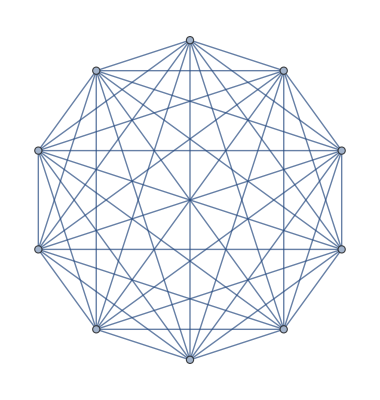

{1<->2,1<->3,1<->4,1<->5,1<->6,1<->7,1<->8,1<->9,1<->10,2<->3,2<->4,2<->5,2<->6,2<->7,2<->8,2<->9,2<->10,3<->4,3<->5,3<->6,3<->7,3<->8,3<->9,3<->10,4<->5,4<->6,4<->7,4<->8,4<->9,4<->10,5<->6,5<->7,5<->8,5<->9,5<->10,6<->7,6<->8,6<->9,6<->10,7<->8,7<->9,7<->10,8<->9,8<->10,9<->10}

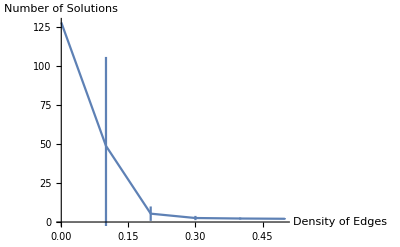

```mathematica
G=DGRandomMDGP[10]["G"]
nSample=25;
density={0,0.1,0.2,0.3,0.4,0.5}; (* density of edges *)
(* generating sample data *)
Needs["ErrorBarPlots`"]
allEdges=EdgeList[G]
nSols=Table[0,{ii,Length[density]},{jj,nSample}];
g=Table[0,{ii,Length[density]},{jj,nSample}];
For[ii=1,ii≤Length[density],ii++,
d=density[[ii]];
For[jj=1,jj≤nSample,jj++,
(* create subgraph *)
gij=G;
For[kk=1,kk≤Length[allEdges],kk++,
ek=allEdges[[kk]];
If[RandomReal[]>d&&Abs[ek[[1]]-ek[[2]]]>3,gij=EdgeDelete[gij,ek]]
];
g[[ii]][[jj]]=gij;
(* solve instance *)
nodes=Table[ii,{ii,Length[VertexList[gij]]}];
{S,work}=DGBPSolver[gij,nodes];
nSols[[ii]][[jj]]=Length[S["Points"]];
];
];
(* plot results *)
ErrorListPlot[Table[{{density[[ii]],Mean[nSols[[ii]]]},ErrorBar[StandardDeviation[nSols[[ii]]]]},{ii,Length[density]}],
Joined->True,
AxesLabel->{"Density of Edges", "Number of Solutions"}]
```

IBPSolver

## Source Code

```mathematica
ClearAll[DGIPBSubG,DGIBPSolver];

DGIPBSubG[G_,kk_,branch_,nslices_]:=Module[{ii,E,W=G,nodes,ei,ej,dij,lij,uij},
(* Delete vertices k+1,...,numberOfAtoms *)
nodes=Table[ii,{ii,kk+1,Length[VertexList[G]]}];
W=VertexDelete[G,nodes];
E=EdgeList[W];
dij=Table[0,{ii,Length[E]}];
lij=Table[0,{ii,Length[E]}];
uij=Table[0,{ii,Length[E]}];
For[ii=1,ii≤Length[E],ii++,
{lij[[ii]],uij[[ii]]}=DGEdgeDistanceBounds[G,E[[ii]]];
dij[[ii]]=DGEdgeWeight[G,E[[ii]]];
(* set weight affected by branch *)
ei=E[[ii]][[1]];
ej=E[[ii]][[2]];
If[ei>ej,{ei,ej}={ej,ei}];
If[ej-ei==3,
dij[[ii]]=(uij[[ii]]-lij[[ii]])/nslices;
dij[[ii]]=dij[[ii]]*branch[[ej]]+lij[[ii]]+dij[[ii]]/2.0;
];
];
W=Graph[E,EdgeWeight->dij];
For[ii=1,ii≤Length[E],ii++,
PropertyValue[{W,E[[ii]]}, "DistanceBounds"] = {lij[[ii]],uij[[ii]]};
];
Return[W];
];

DGIBPSolver[G_,nslices_,verbose_:False]:=
(* Calculate all solutions of the DMDGP instance defined by the graph G using natural ordering. *)
Module[
(* local variables *)
{ii,kk,numberOfAtoms,prune,branch,W,S,SW,work,locwork,tol=10^(-5)},
numberOfAtoms=Length[VertexList[G]];
(* init IBPTree *)
branch=Table[0,{ii,numberOfAtoms}];branch[[1;;3]]=nslices-1;
work=Table[0,{ii,numberOfAtoms}];work[[1;;3]]=1;
(* solutions and branches *)
S=<|"Points"->{},"Branches"->{}|>;
kk=4;
While[kk>3,
W=DGIPBSubG[G,kk,branch,nslices];
{SW,locwork}=DGBPSolver[W,DGNaturalOrdering[W],kk≠numberOfAtoms];
For[ii=4,ii≤kk,ii++,work[[ii]]+=locwork[[ii]]];
prune=Length[SW["Points"]]==0; (* unfeasible subgraph *)
(*Print["[ibp] k=",k,"  branch=",branch, "   work=",work," prune=",prune];*)
(* solution found *)
If[Not[prune]&&kk==numberOfAtoms ,
S["Points"]=Join[S["Points"],SW["Points"]];
AppendTo[S["Branches"],branch]];
(* update tree node *)
prune=prune||kk==Length[branch];
If[prune&&branch[[kk]]==nslices-1,
While[kk>3&&branch[[kk]]==nslices-1,kk--];
];
If[prune&&branch[[kk]]<nslices-1,
branch[[kk]]++;
For[ii=kk+1,ii≤Length[branch],ii++,branch[[ii]]=0];
];
If[Not[prune],kk++];
];
If[verbose,
Print["DGIBPSolver"];
Print["Number of solutions: ",Length[S["Points"]]]
];
Return[{S,work}]
];
```

## Examples and Applications

### Check DGIBPSolver

```mathematica
P=DGRandomMDGP[5,0.1,5.0];
branch={1,1,1,1,0};
nslices=2;
W=DGIPBSubG[P["G"],4,branch,nslices];
DGPrintGraph[P["G"]];
DGPrintGraph[W];
```

| ii | jj | dij | lij | uij
1 | 1 | 2 | 1.526 | 1.526 | 1.526
2 | 1 | 3 | 2.49139 | 2.49139 | 2.49139
3 | 1 | 4 | 3.83767 | 3.4539 | 4.22143
4 | 1 | 5 | 4.36545 | 3.9289 | 4.80199
5 | 2 | 3 | 1.526 | 1.526 | 1.526
6 | 2 | 4 | 2.49139 | 2.49139 | 2.49139
7 | 2 | 5 | 2.94646 | 2.65181 | 3.24111
8 | 3 | 4 | 1.526 | 1.526 | 1.526
9 | 3 | 5 | 2.49139 | 2.49139 | 2.49139
10 | 4 | 5 | 1.526 | 1.526 | 1.526

| ii | jj | dij | lij | uij
1 | 1 | 2 | 1.526 | 1.526 | 1.526
2 | 1 | 3 | 2.49139 | 2.49139 | 2.49139
3 | 1 | 4 | 4.02955 | 3.4539 | 4.22143
4 | 2 | 3 | 1.526 | 1.526 | 1.526
5 | 2 | 4 | 2.49139 | 2.49139 | 2.49139
6 | 3 | 4 | 1.526 | 1.526 | 1.526

### Solving a small instance using DGIBP

```mathematica
P=DGRandomMDGP[5,0.1,5.0];
DGPrintGraph[P["G"]]
```

| ii | jj | dij | lij | uij
1 | 1 | 2 | 1.526 | 1.526 | 1.526
2 | 1 | 3 | 2.49139 | 2.49139 | 2.49139
3 | 1 | 4 | 2.9333 | 2.63997 | 3.22663
4 | 1 | 5 | 2.70031 | 2.43028 | 2.97034
5 | 2 | 3 | 1.526 | 1.526 | 1.526
6 | 2 | 4 | 2.49139 | 2.49139 | 2.49139
7 | 2 | 5 | 3.07284 | 2.76556 | 3.38013
8 | 3 | 4 | 1.526 | 1.526 | 1.526
9 | 3 | 5 | 2.49139 | 2.49139 | 2.49139
10 | 4 | 5 | 1.526 | 1.526 | 1.526

```mathematica
nslices=2; (* testing increasing the the number of slices*)
{S,work}=DGIBPSolver[P["G"],nslices,True];
```

DGIBPSolver

Number of solutions: 0

```mathematica
nslices=3; (* increasing the number of slices *)
{S,work}=DGIBPSolver[P["G"],nslices,True];
```

DGIBPSolver

Number of solutions: 2

### Illustrating the tree exponential growth

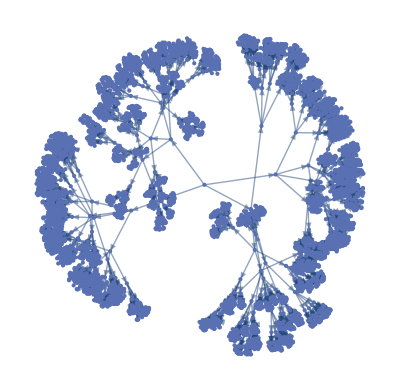

Number of Vertex=5461

```mathematica
(* Plot IBP Tree (it can be very slow!!!) *)
numberOfAtoms=9;
numberOfSlices=2; (* or 2 at max *)
node=3;
edges={};
count=3;
For[ii=1,ii≤2*numberOfSlices,ii++,
AppendTo[edges,node->(++count)]
];
T=TreeGraph[edges];
For[kk=5,kk≤numberOfAtoms,kk++,
leafs=Select[VertexList[T],VertexDegree[T,#]===1&];
count=Max[VertexList[T]];
For[ii=1,ii≤Length[leafs],ii++,
node=leafs[[ii]];
For[jj=1,jj≤2*numberOfSlices,jj++,
AppendTo[edges,node->(++count)]
]
];
T=TreeGraph[edges];
]
Print[T]
Print["Number of Vertex=",Length[VertexList[T]]]
```

```mathematica
(* Number of nodes on IBP tree *)
NumberOfIBPVertex[numberOfAtoms_,numberOfSlices_]:=Module[{},((2*numberOfSlices)^(numberOfAtoms-2)-1)/((2*numberOfSlices)-1)];
NumberOfIBPVertex[9,1]
```

127

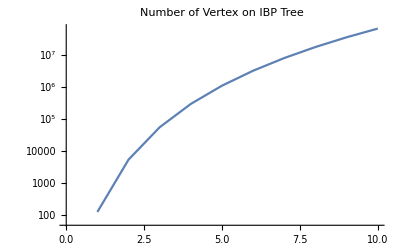

```mathematica
xy=Table[{ii,NumberOfIBPVertex[9,ii]},{ii,10}];
ListLogPlot[xy,Joined->True,PlotLabel->"Number of Vertex on IBP Tree"]
```

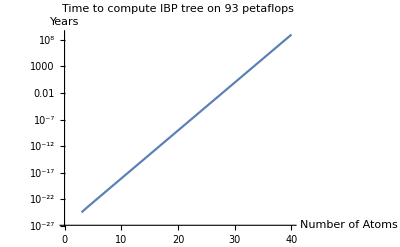

```mathematica
(* Top 1: Sunway TaihuLight at 93 petaflops (10^15 flops) on November 2016 *)
xy=Table[{ii,NumberOfIBPVertex[ii,4]/(365*24*3600*(93*10^15))},{ii,40}];
ListLogPlot[xy,Joined->True,PlotLabel->"Time to compute IBP tree on 93 petaflops",AxesLabel->{"Number of Atoms","Years"}]
```

## 4) BP with AGC

### Inicializa pacote clifford.m

```mathematica
<< clifford.m;
```

### Define modelo conforme

```mathematica
(* define assinatura do espaço R^(p,q), onde p+q = n *)
n=3;
p=n+1;
q=1;
$SetSignature=p;
e0=0.5*(e[p+1]-e[p]);
einf=e[p+1]+e[p];
```

## Source Code

```mathematica
ClearAll[IntersEsferasAGC,DGIntersect3SpheresCGA,DGBPGetXCGA,DGBPSolverCGA];
(* modulo interseção usando AGC*)IntersEsferasAGC[ca_,cb_,cc_,da_,db_,dc_,e0_,einf_]:=Module[{epsilon,p,A,d,ii,jj,TEsferas,ri,Ci,ci,sigmai,sigma,a,aa,inva,sigmaN,a2,pto1,Ie,pto2,x1,x2,X,x,y,z,pp,eqSigma,erro},
epsilon=5;
p=3+1;
(*Print["n = ", Style[p-1,Red]];*)
A=Table[0,{ii,n},{jj,n}];
d=Table[0,{ii,n},{jj,1}];
(*Print["ca = ",Style[ca,Red],",  cb = ",Style[cb,Red],",  cc = ",Style[cc,Red]];
Print["da = ",Style[da,Red],",  db = ",Style[db,Red],",  dc = ",Style[dc,Red]];*)
A[[;;,1]]=ca;
A[[;;,2]]=cb;
A[[;;,3]]=cc;
d[[1,1]]=da;
d[[2,1]]=db;
d[[3,1]]=dc;
(*Print["A = ", Style[MatrixForm[A],Red],", d = ",Style[MatrixForm[d],Red]];*)
(*define esferas no espaco conforme*)
TEsferas={};
For[ii=1,ii≤n,ii++,
ri=d[[ii,1]];Ci=ToBasis[A[[;;,ii]]];
ci=e0+Ci+(0.5*Norm[ToVector[Ci,p+1]]^2)*einf;
sigmai=ci-(0.5*ri^2)*einf;
TEsferas=AppendTo[TEsferas,sigmai];
];
(*computa intersecao usando produto exterior*)
sigma=TEsferas[[1,;;]];
For[ii=2,ii≤n,ii++,
sigma=Chop[OuterProduct[sigma,TEsferas[[ii,;;]]],10^(-epsilon)];];
(*normaliza sigma*)
a=Chop[InnerProduct[einf,sigma],10^(-epsilon)];
(*calcula inversa de a,obs:o programa da erro,as vezes*)
aa=Chop[GeometricProduct[a,a],10^(-epsilon)];
inva=Chop[GeometricProduct[a,MultivectorInverse[aa]],10^(-epsilon)];
sigmaN=-Chop[GeometricProduct[sigma,inva],10^(-epsilon)];
(*(*obtem:sigmaN^2*)Print["σ_n^2 = ",Style[Chop[GeometricProduct[sigmaN,sigmaN],10^(-2)],Red]];
(*obtem:einf.sigmaN=-1*)Print["e∞.σ_n = ",Style[Chop[InnerProduct[einf,sigmaN],10^(-2)],Red]];*)(*obtem:extrais pontos do par de ptos*)
a2=Chop[InnerProduct[einf,Dual[sigma,p+1]],10^(-epsilon)];
pto1=Chop[-GeometricProduct[Sqrt[InnerProduct[Dual[sigma,p+1],Dual[sigma,p+1]]]+Dual[sigma,p+1],MultivectorInverse[a2]],10^(-epsilon)];
Ie=OuterProduct[einf,e0];
pto2=Chop[GeometricProduct[Sqrt[InnerProduct[Dual[sigma,p+1],Dual[sigma,p+1]]]-Dual[sigma,p+1],MultivectorInverse[a2]],10^(-epsilon)];
x1=GeometricProduct[OuterProduct[pto1,Ie],Ie];
x2=GeometricProduct[OuterProduct[pto2,Ie],Ie];
(*Print["Soluções: x1 = ",Style[MatrixForm[ToVector[x1[[2;;]]]],Red],",  x2 = ",Style[MatrixForm[ToVector[x2[[2;;]]]],Red]];*)

(*Print["Solucoes: "];
Print["x_1 =",Style[x1,Red]," ∈ R^",Style[n,Red]];
Print["x_2 =",Style[x2,Red]," ∈ R^",Style[n,Red]];*)(*calcula erro da solução encontrada*)(*erro=erroMDE[ToVector[x1[[2;;]]],A,d,m];*)
(*Print["erro = ",Style[erro,Red]];*)
(*Print["Erro de x1 = ",Style[erro,Red]];
Print["Erro de x2 = ",Style[erroMDE[ToVector[x2[[2;;]]],A,d,m],Red]];*)
erro=0;
 Return[{ToVector[x1[[2;;]]],ToVector[x2[[2;;]]],erro}];
];

DGIntersect3SpheresCGA[a_,ra_,b_,rb_,c_,rc_,e0_,einf_]:=
(* Gets the 2 solutions of {||x-a||=ra,||x-b||=rb,||x-c||=rc};
   Input;
   a,b,c: sphere centers;
   ra,rb,rc: respective sphere radius;
   Output;   
   x: the two intersections (x[[1]]: positive chirality and x[[2]]: negative chirality);
 *)
Module[{n,A,x,x1,x2,p,dp,u,v,w,du,dv,dw,dpu,AbsCos,error},

(*Print["a=",a,"  ra=",ra,"  b=",b,"  rb=",rb,"  c=",c,"  rc=",rc];*)
{x1,x2, error} = IntersEsferasAGC[a,b,c,ra,rb,rc,e0,einf];

x={x1[[;;]],x2[[;;]]};
Return[{x,error}];
];

DGBPGetXCGA[G_,X_,branch_,nodes_,ii_,e0_,einf_]:=Module[
{jj,kk,neighs,x,error,i1,i2,i3,d1,d2,d3},
kk=nodes[[ii]];
neighs=Intersection[AdjacencyList[G,kk],nodes[[1;;(ii-1)]]];
If[Length[neighs]<3,Throw["InvalidOrder: There is not enough neighs to set a basis"]];
(*Print["neighs=",neighs," k=",k];*)
{i1,i2,i3}=neighs[[1;;3]];
{d1,d2,d3}=DGEdgeWeight[G,{i1<->kk,i2<->kk,i3<->kk}];
{x,error}=DGIntersect3SpheresCGA[X[[i1]],d1,X[[i2]],d2,X[[i3]],d3,e0,einf];
Return[x[[branch+1]]];
];

DGBPSolverCGA[G_,nodes_,onesol_:False,verbose_:False,e0_,einf_]:=
(* Calculate all solutions of the DMDGP instance defined by the graph G. *)
Module[
(* local variables *)
{ii,kk,numberOfAtoms,prune,branch,X,S,work,error,tol=10^(-5)},
numberOfAtoms=Length[VertexList[G]];
X=DGBPXinit[G,nodes[[1;;3]]];
(* init BPTree *)
branch=Table[0,{ii,numberOfAtoms}];branch[[1;;3]]=1;
work=Table[0,{ii,numberOfAtoms}];work[[1;;3]]=1;
(* solutions and branches *)
S=<|"Points"->{},"Branches"->{}|>;
kk=4;
While[kk>3,
work[[kk]]++;
X[[nodes[[kk]]]]=DGBPGetXCGA[G,X,branch[[kk]],nodes,kk,e0,einf];
error=DGRelativeResidue[G,X,nodes,kk];
prune=error>tol;
(*Print["[bp] k=",k,"  branch=",branch,"  error=",NumberForm[error,{3,2}],"  prune=",prune];*)
(*DGPrintX[X[[nodes[[1;;k]]]]];*)
(* solution found *)
If[Not[prune]&&kk==numberOfAtoms ,
AppendTo[S["Points"],X];
AppendTo[S["Branches"],branch];
If[onesol,
Return[{S,work}];
];
];
(* update tree node *)
prune=prune||kk==Length[branch];
If[prune&&branch[[kk]]==1,
While[kk>3&&branch[[kk]]==1,kk--];
];
If[prune&&branch[[kk]]==0,
branch[[kk]]=1;
For[ii=kk+1,ii≤Length[branch],ii++,branch[[ii]]=0];
];
If[Not[prune],kk++];
];
If[verbose,
Print["StyleBox[\"DGBPSolver CGA\",FontSlant->\"Italic\",\nFontVariations->{\"Underline\"->True}]"];
Print["Number of solutions: ",Style[Length[S["Points"]],Red]];
];
Return[{S,work}];
];
```

## Examples and Application (AGC version)

### Exemplo simples

```mathematica
(* Creates a DGProblem with specific edges *)
x = {{0, 0, 0}, {-1, 0, 0}, {-1.5,Sqrt[3]/2, 0}, {-1.311,1.552,0.702}, {-0.779,2.368,0.474}};
eij = {1<->2, 1<->3, 1<->4,2<->3,2<->4,2<->5,3<->4,3<->5,4<->5};
P = DGProblem[x, eij];
G =P["G"];
PropertyValue[{G, 2<->5}, EdgeWeight]=2.575;
PropertyValue[{G, 2<->5}, "DistanceBounds"]={2.2,2.6};
nodes={1,2,3,4,5};
DGPrintGraph[G];
{S7,work}=DGBPSolverCGA[G,nodes,False,True,e0,einf];
Print["Soluções: ",Style[S7["Points"],Red]];
```

| ii | jj | dij | lij | uij
1 | 1 | 2 | 1. | 1. | 1.
2 | 1 | 3 | 1.73205 | 1.73205 | 1.73205
3 | 1 | 4 | 2.14947 | 2.14947 | 2.14947
4 | 2 | 3 | 1. | 1. | 1.
5 | 2 | 4 | 1.73154 | 1.73154 | 1.73154
6 | 2 | 5 | 2.575 | 2.2 | 2.6
7 | 3 | 4 | 0.999543 | 0.999543 | 0.999543
8 | 3 | 5 | 1.73218 | 1.73218 | 1.73218
9 | 4 | 5 | 1.00043 | 1.00043 | 1.00043

DGBPSolver CGA

Number of solutions: 4

Soluções: {{{0,0,0},{-1.,0,0},{-1.5,0.866025,0},{-1.311,1.552,-0.702},{-2.06431,2.05876,-1.12223}},{{0,0,0},{-1.,0,0},{-1.5,0.866025,0},{-1.311,1.552,-0.702},{-1.26451,2.52052,-0.455678}},{{0,0,0},{-1.,0,0},{-1.5,0.866025,0},{-1.311,1.552,0.702},{-1.26451,2.52052,0.455678}},{{0,0,0},{-1.,0,0},{-1.5,0.866025,0},{-1.311,1.552,0.702},{-2.06431,2.05876,1.12223}}}

### Small Instance CGA

```mathematica
edges={{1,2},{1,3},{1,4},{1,6},
{2,3},{2,4},{2,5},
{3,4},{3,5},{3,6},
{4,5},{4,6},{4,7},
{5,6},{5,7},
{6,7}};
X=DGRandom3DBackbone[7];
P=DGProblem[X["Points"],edges];
X=P["X"];
G=P["G"];
DGPrintGraph[G];
nodes=Table[ii,{ii,Length[VertexList[G]]}]
(*{S,work}=DGBPSolver[G,nodes,False,True];*)
{S,work}=DGBPSolverCGA[G,nodes,False,True,e0,einf];
Print["Soluções: ",Style[S["Points"],Red]];
X=S["Points"];
B=S["Branches"];
DGPlot3DBackbone[X[[1]],.2,.08]
DGPlot3DBackbone[X[[2]],.2,.08]
```

| ii | jj | dij | lij | uij
1 | 1 | 2 | 1.526 | 1.526 | 1.526
2 | 1 | 3 | 2.49139 | 2.49139 | 2.49139
3 | 1 | 4 | 2.94759 | 2.94759 | 2.94759
4 | 1 | 6 | 2.91615 | 2.91615 | 2.91615
5 | 2 | 3 | 1.526 | 1.526 | 1.526
6 | 2 | 4 | 2.49139 | 2.49139 | 2.49139
7 | 2 | 5 | 2.90043 | 2.90043 | 2.90043
8 | 3 | 4 | 1.526 | 1.526 | 1.526
9 | 3 | 5 | 2.49139 | 2.49139 | 2.49139
10 | 3 | 6 | 2.95634 | 2.95634 | 2.95634
11 | 4 | 5 | 1.526 | 1.526 | 1.526
12 | 4 | 6 | 2.49139 | 2.49139 | 2.49139
13 | 4 | 7 | 2.903 | 2.903 | 2.903
14 | 5 | 6 | 1.526 | 1.526 | 1.526
15 | 5 | 7 | 2.49139 | 2.49139 | 2.49139
16 | 6 | 7 | 1.526 | 1.526 | 1.526

{1,2,3,4,5,6,7}

DGBPSolver CGA

Number of solutions: 4

Soluções: {{{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-1.57599,2.139,-1.2764},{-2.09679,1.37399,-2.48974},{-1.4848,-0.0237719,-2.50973},{-1.83848,-0.751474,-1.21589}},{{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-1.57599,2.139,-1.2764},{-2.09679,1.37399,-2.48974},{-1.4848,-0.0237719,-2.50973},{0.0365217,0.0885635,-2.55033}},{{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-1.57599,2.139,1.2764},{-2.09679,1.37399,2.48974},{-1.4848,-0.0237719,2.50973},{0.0365217,0.0885635,2.55033}},{{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-1.57599,2.139,1.2764},{-2.09679,1.37399,2.48974},{-1.4848,-0.0237719,2.50973},{-1.83848,-0.751474,1.21589}}}

-Graphics3D-

-Graphics3D-

### Easy case using natural order CGA

```mathematica
P=DGRandomMDGP[20,0.0,5];
nodes=DGNaturalOrdering[P["G"]];
timeElapsed=Timing[{S,work}=DGBPSolverCGA[P["G"],nodes,False,True,e0,einf]][[1]];
Print["TimeElapsed=",timeElapsed];
DGRelativeResidue[P["G"],S["Points"][[1]],True];
```

DGBPSolver CGA

Number of solutions: 2

TimeElapsed=6.19324

Solution Quality

Number of nodes      : 20

Number of edges      : 81

Relative error bounds: {0.,1.03538×10^-6}

Mean relative error  : 1.94565×10^-8

### Instance with more than two solutions CGA

```mathematica
x=RandomReal[1,{6,3}];
edges=DGEdgesMDGP[Length[x]];
(*AppendTo[edges,1\[UndirectedEdge]6]*)
P=DGProblem[x,edges];
nodes=DGNaturalOrdering[P["G"]];
{S,work}=DGBPSolverCGA[P["G"],nodes,False,True,e0,einf];
```

DGBPSolver CGA

Number of solutions: 8

### Comparando o BuildUpSolver, BPSolver e BPSolver com AGC (n = 10, ..., 100)

- - - - -  - - - - - - - - - - - - -

- - - - -  - - - - - - - - - - - - -

- - - - - Dados do BPSolver - - - - -

DGBPSolver

Number of solutions: 2

Solution Quality

Number of nodes      : 10

Number of edges      : 39

Relative error bounds: {0.,8.87596×10^-15}

Mean relative error  : 6.73833×10^-16

- - - - -  - - - - - - - - - - - - - - - - -

- - - - -  - - - - - - - - - - - - - - - - -

- - - - - Dados do BPSolver com CGA - - - - -

DGBPSolver CGA

Number of solutions: 2

Solution Quality

Number of nodes      : 10

Number of edges      : 39

Relative error bounds: {0.,9.45799×10^-15}

Mean relative error  : 1.11285×10^-15

- - - - -  - - - - - - - - - - - - -

- - - - -  - - - - - - - - - - - - -

- - - - - Dados do BPSolver - - - - -

DGBPSolver

Number of solutions: 2

Solution Quality

Number of nodes      : 20

Number of edges      : 116

Relative error bounds: {0.,6.74719×10^-12}

Mean relative error  : 3.18568×10^-13

- - - - -  - - - - - - - - - - - - - - - - -

- - - - -  - - - - - - - - - - - - - - - - -

- - - - - Dados do BPSolver com CGA - - - - -

DGBPSolver CGA

Number of solutions: 2

Solution Quality

Number of nodes      : 20

Number of edges      : 116

Relative error bounds: {0.,3.93591×10^-11}

Mean relative error  : 1.91098×10^-12

- - - - -  - - - - - - - - - - - - -

- - - - -  - - - - - - - - - - - - -

- - - - - Dados do BPSolver - - - - -

DGBPSolver

Number of solutions: 2

Solution Quality

Number of nodes      : 30

Number of edges      : 187

Relative error bounds: {0.,8.52093×10^-13}

Mean relative error  : 4.78912×10^-14

- - - - -  - - - - - - - - - - - - - - - - -

- - - - -  - - - - - - - - - - - - - - - - -

- - - - - Dados do BPSolver com CGA - - - - -

DGBPSolver CGA

Number of solutions: 2

Solution Quality

Number of nodes      : 30

Number of edges      : 187

Relative error bounds: {0.,3.78829×10^-10}

Mean relative error  : 2.46706×10^-11

- - - - -  - - - - - - - - - - - - -

- - - - -  - - - - - - - - - - - - -

- - - - - Dados do BPSolver - - - - -

DGBPSolver

Number of solutions: 2

Solution Quality

Number of nodes      : 40

Number of edges      : 326

Relative error bounds: {0.,1.31215×10^-11}

Mean relative error  : 3.3979×10^-13

- - - - -  - - - - - - - - - - - - - - - - -

- - - - -  - - - - - - - - - - - - - - - - -

- - - - - Dados do BPSolver com CGA - - - - -

DGBPSolver CGA

Number of solutions: 2

Solution Quality

Number of nodes      : 40

Number of edges      : 326

Relative error bounds: {0.,1.19758×10^-8}

Mean relative error  : 3.07255×10^-10

- - - - -  - - - - - - - - - - - - -

- - - - -  - - - - - - - - - - - - -

- - - - - Dados do BPSolver - - - - -

DGBPSolver

Number of solutions: 2

Solution Quality

Number of nodes      : 50

Number of edges      : 382

Relative error bounds: {0.,3.7536×10^-11}

Mean relative error  : 9.63099×10^-13

- - - - -  - - - - - - - - - - - - - - - - -

- - - - -  - - - - - - - - - - - - - - - - -

- - - - - Dados do BPSolver com CGA - - - - -

DGBPSolver CGA

Number of solutions: 2

Solution Quality

Number of nodes      : 50

Number of edges      : 382

Relative error bounds: {0.,1.96736×10^-9}

Mean relative error  : 3.56679×10^-11

- - - - -  - - - - - - - - - - - - -

- - - - -  - - - - - - - - - - - - -

- - - - - Dados do BPSolver - - - - -

DGBPSolver

Number of solutions: 2

Solution Quality

Number of nodes      : 60

Number of edges      : 615

Relative error bounds: {0.,3.25036×10^-11}

Mean relative error  : 2.06726×10^-13

- - - - -  - - - - - - - - - - - - - - - - -

- - - - -  - - - - - - - - - - - - - - - - -

- - - - - Dados do BPSolver com CGA - - - - -

DGBPSolver CGA

Number of solutions: 2

Solution Quality

Number of nodes      : 60

Number of edges      : 615

Relative error bounds: {0.,2.6468×10^-10}

Mean relative error  : 1.93385×10^-12

- - - - -  - - - - - - - - - - - - -

- - - - -  - - - - - - - - - - - - -

- - - - - Dados do BPSolver - - - - -

DGBPSolver

Number of solutions: 2

Solution Quality

Number of nodes      : 70

Number of edges      : 651

Relative error bounds: {0.,9.76403×10^-11}

Mean relative error  : 4.91125×10^-12

- - - - -  - - - - - - - - - - - - - - - - -

- - - - -  - - - - - - - - - - - - - - - - -

- - - - - Dados do BPSolver com CGA - - - - -

DGBPSolver CGA

Number of solutions: 2

Solution Quality

Number of nodes      : 70

Number of edges      : 651

Relative error bounds: {0.,1.40297×10^-8}

Mean relative error  : 4.947×10^-10

- - - - -  - - - - - - - - - - - - -

- - - - -  - - - - - - - - - - - - -

- - - - - Dados do BPSolver - - - - -

DGBPSolver

Number of solutions: 2

Solution Quality

Number of nodes      : 80

Number of edges      : 772

Relative error bounds: {0.,3.24741×10^-9}

Mean relative error  : 3.79702×10^-11

- - - - -  - - - - - - - - - - - - - - - - -

- - - - -  - - - - - - - - - - - - - - - - -

- - - - - Dados do BPSolver com CGA - - - - -

DGBPSolver CGA

Number of solutions: 2

Solution Quality

Number of nodes      : 80

Number of edges      : 772

Relative error bounds: {0.,1.20085×10^-8}

Mean relative error  : 1.42059×10^-10

- - - - -  - - - - - - - - - - - - -

- - - - -  - - - - - - - - - - - - -

- - - - - Dados do BPSolver - - - - -

DGBPSolver

Number of solutions: 2

Solution Quality

Number of nodes      : 90

Number of edges      : 887

Relative error bounds: {0.,4.63871×10^-6}

Mean relative error  : 1.71047×10^-8

- - - - -  - - - - - - - - - - - - - - - - -

- - - - -  - - - - - - - - - - - - - - - - -

- - - - - Dados do BPSolver com CGA - - - - -

DGBPSolver CGA

Number of solutions: 1

Solution Quality

Number of nodes      : 90

Number of edges      : 887

Relative error bounds: {0.,8.2754×10^-6}

Mean relative error  : 3.0579×10^-8

- - - - -  - - - - - - - - - - - - -

- - - - -  - - - - - - - - - - - - -

- - - - - Dados do BPSolver - - - - -

DGBPSolver

Number of solutions: 2

Solution Quality

Number of nodes      : 100

Number of edges      : 1033

Relative error bounds: {0.,2.1875×10^-7}

Mean relative error  : 8.63031×10^-10

- - - - -  - - - - - - - - - - - - - - - - -

- - - - -  - - - - - - - - - - - - - - - - -

- - - - - Dados do BPSolver com CGA - - - - -

DGBPSolver CGA

Number of solutions: 2

Solution Quality

Number of nodes      : 100

Number of edges      : 1033

Relative error bounds: {0.,3.18877×10^-7}

Mean relative error  : 1.27314×10^-9

Erros BuilpUP = {}

Erros BP = {6.73833×10^-16,3.18568×10^-13,4.78912×10^-14,3.3979×10^-13,9.63099×10^-13,2.06726×10^-13,4.91125×10^-12,3.79702×10^-11,1.71047×10^-8,8.63031×10^-10}

Erros BP CGA = {1.11285×10^-15,1.91098×10^-12,2.46706×10^-11,3.07255×10^-10,3.56679×10^-11,1.93385×10^-12,4.947×10^-10,1.42059×10^-10,3.0579×10^-8,1.27314×10^-9}

-Graphics-

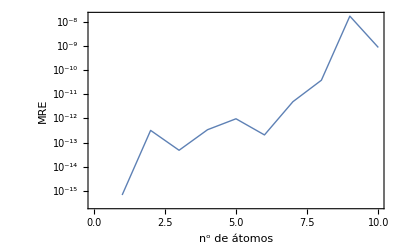

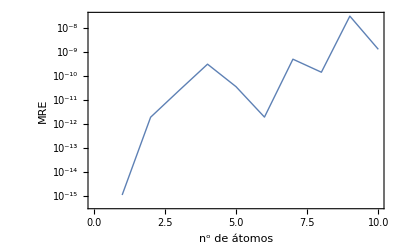

```mathematica
ListaErrosBuildUP={};
ListaErrosBP={};
ListaErrosBPCGA={};
eerroBuildUP= 0;
eerroBP= 0;
eerroBPCGA= 0;

For[natoms=10, natoms≤100,natoms=natoms+10,
(*natoms=10;*)
P=DGRandomMDGP[natoms,0.0,5.0,0];
X=P["X"];
G=P["G"];
nodes=Table[ii,{ii,Length[VertexList[G]]}];
(*extra*)

(*Print["- - - - -  - - - - - - - - - - - - - - - -"];
Print["- - - - -  - - - - - - - - - - - - - - - -"];
Print["- - - - -  Dados do BuildUpSolver - - - - -"];
X=DGBuildUpSolver[G,nodes];
eerroBuildBP=DGRelativeResidue[G,X,True][[2]];
ListaErrosBuildUP=AppendTo[ListaErrosBuildUP,eerroBuildBP];
(*DGMDEE[G,X]*)
(*Print["Solução : ", Style[X,Red]];*)
*)

Print["- - - - -  - - - - - - - - - - - - -"];
Print["- - - - -  - - - - - - - - - - - - -"];
Print["- - - - - Dados do BPSolver - - - - -"];
{XBP,workBP}=DGBPSolver[G,nodes,False,True];
eerroBP=DGRelativeResidue[G,XBP["Points"][[1]],True][[2]];
ListaErrosBP=AppendTo[ListaErrosBP,eerroBP];
(*Print["Solução 1: ", Style[XBP["Points"][[1]],Red]];*)
(*Print["Solução 2: ", Style[XBP["Points"][[2]],Red]];*)
(*GraphicsGrid[{{DGPlot3DBackbone[XBP["Points"][[1]],.2,0.1],DGPlot3DBackbone[XBP["Points"][[2]],.2,0.1]}}]
DGPlot3DBackbone[X,.2,0.1]*)

Print["- - - - -  - - - - - - - - - - - - - - - - -"];
Print["- - - - -  - - - - - - - - - - - - - - - - -"];
Print["- - - - - Dados do BPSolver com CGA - - - - -"];
{XBP,workBP}=DGBPSolverCGA[G,nodes,False,True,e0,einf];
eerroBPCGA= DGRelativeResidue[G,XBP["Points"][[1]],True][[2]];
ListaErrosBPCGA=AppendTo[ListaErrosBPCGA,eerroBPCGA];
(*Print["Solução 1: ", Style[XBP["Points"][[1]],Red]];
Print["Solução 2: ", Style[XBP["Points"][[2]],Red]];*)
(*GraphicsGrid[{{DGPlot3DBackbone[XBP["Points"][[1]],.2,0.1],DGPlot3DBackbone[XBP["Points"][[2]],.2,0.1]}}]
DGPlot3DBackbone[X,.2,0.1]*)
(*];*)
];

Print["Erros BuilpUP = ",Style[ListaErrosBuildUP,Red]];Print["Erros BP = ",Style[ListaErrosBP,Red]];Print["Erros BP CGA = ",Style[ListaErrosBPCGA,Red]];

(*plota grafico erros*)
ListLogPlot[ListaErrosBuildUP,Joined->True,PlotStyle->Thick,Frame->True,FrameLabel->{"n^o de átomos","MRE"},FrameStyle->Directive[Black,FontSize->13]]
ListLogPlot[ListaErrosBP,Joined->True,PlotStyle->Thick,Frame->True,FrameLabel->{"n^o de átomos","MRE"},FrameStyle->Directive[Black,FontSize->13]]
ListLogPlot[ListaErrosBPCGA,Joined->True,PlotStyle->Thick,Frame->True,FrameLabel->{"n^o de átomos","MRE"},FrameStyle->Directive[Black,FontSize->13]]
```